# Inverted spherical Pendulum

## Tavola 2-3 Controllo dei Robot

# -Graphics-

## Packages

```mathematica
Directory[];
SetDirectory["/home/alfredo/MATLAB-Drive/Tavole/Hopper2D"];
Get["ScrewCalculusPro.m", Path->"/home/alfredo/MATLAB-Drive/Tavole/Hopper2D"]
Get["ToMatlab.m", Path->"/home/alfredo/MATLAB-Drive/Tavole/Hopper2D"]
```

## Initialization

```mathematica
q[t_]={θr[t],θl[t],ψ[t],ϕ[t]};
qd[t_]=D[q[t],t];
qdd[t_]=D[qd[t],t];
```

```mathematica
params = {G-> 9.81,mp->1.,ma->1 ,mr-> 0.5,lp-> 0.7,la-> 1,  r-> 0.3, Ia-> 0.8 };
```

## Vincolo di Rotolamento senza strisciamento

```mathematica
θ=r/la(q[t][[1]]-q[t][[2]]);
xd=r/2*Cos[θ]*(qd[t][[1]]+qd[t][[2]]);
yd=r/2*Sin[θ]*(qd[t][[1]]+qd[t][[2]]);
```

## Kinematics

```mathematica
va={xd,yd,0};
wrr={θr'[t],0,D[θ,t]};
wrl={θl'[t],0,D[θ,t]};
vrr=θr'[t]*r;
vrl=θl'[t]*r;
```

```mathematica
Rz[ϵ_]=RotationMatrix[ϵ,{0,0,1}];
Ry[ϵ_]=RotationMatrix[ϵ,{0,1,0}];
Rx[ϵ_]=RotationMatrix[ϵ,{1,0,0}];
Rp=Rx[ψ[t]].Ry[ϕ[t]].Rz[η[t]];
```

Parametrizzo la rotazione come XYZ:  θ lungo X,   ψ  lungo Y e  ϕ lungo Z

```mathematica
AP=Rp.{0,0,lp/2};
dAP=D[AP,t];
```

```mathematica
Subscript[wP, g]= ψ'[t]*{1,0,0}+ϕ'[t]*Rx[ψ[t]].{0,1,0}+η'[t]*Rx[ψ[t]].Ry[ϕ[t]].{0,0,1};
Subscript[wP, p]=η'[t]*{0,0,1}+ϕ'[t]*Transpose[Rz[η[t]]].{0,1,0}+ψ'[t]*Transpose[Ry[ϕ[t]].Rz[η[t]]].{1,0,0};
```

```mathematica
Subscript[wP, s]=Rp.Subscript[wP, p];
vP=va+Subscript[wP, s] × AP;
```

```mathematica
Jr={{1/2*mr*r^2,0,0},{0,1/4*mr*r^2,0},{0,0,1/4*mr*r^2}};
Jp={{1/12*mp*lp^2,0,0},{0,1/12*mp*lp^2,0},{0,0,0}};
```

```mathematica
Jpg=Simplify[Rp.Jp.Transpose[Rp]];
```

## Kinetics Energy

#### Pendulum

```mathematica
Ep1=Simplify[1/2*mp*vP.vP];
Ep2=Simplify[1/2*Subscript[wP, s].Jpg.Subscript[wP, s]];
```

#### Axes

```mathematica
Ea1=1/2*mp*va.va;
Ea2=1/2*Ia*θ*θ;
```

#### Wheels

```mathematica
Ewl1=1/2*mr*vrr^2;
Ewr1=1/2*mr*vrl^2;
Ewl2=1/2*wrr.Jr.wrr;
Ewr2=1/2*wrl.Jr.wrl;
```

```mathematica
Etot=Simplify[Ewl1+Ewl2+Ewr1+Ewr2+Ep1+Ep2];
```

## Potential Energy and Lagrangian

```mathematica
U=mp*G*AP[[3]];
L = Etot-U;
Emec=Etot+U;
```

## Equations of Motion

```mathematica
DynLeftTerm = Simplify[D[D[L,{qd[t]}],t]-D[L,{q[t]}]];
```

```mathematica
Mq = Simplify[D[DynLeftTerm,{qdd[t]}]];
Cq = Simplify[InertiaToCoriolis[Mq,q[t],qd[t]]];
Gq = Simplify[DynLeftTerm-Mq.qdd[t]-Cq.qd[t]];
```

## Non-linear analysis tools

#### Lie Brackets

```mathematica
(*Attenzione, sono implementati tutti come vettori riga, bisogna poi trasporre il risultato a seconda di come lo si usa*)
```

```mathematica
LieBracketScalar[f_,λ_,x_]:=D[λ,{x}].f;
LieBracketVector[f_,g_,x_]:=D[g,{x}].f - D[f,{x}].g;
LieBracketCovector[f_,ω_,x_]:=f.Transpose[D[ω,{x}]]+ω.D[f,{x}];
```

TEST

```mathematica
(*x = {x1,x2,x3};
f = {x1,x2^2,x3};
g = {x1^2,x2,x1*x2};
xcol = {{x1},{x2},{x3}};
fcol = {{x1},{x2^2},{x3}};
gcol = {{x1^2},{x2},{x1*x2}};
λ={x1*x2};
ω={x1,x2,x3};
LieBracketScalar[f,λ,{x1,x2,x3}]//MatrixForm
LieBracketVector[f,g,x]//MatrixForm
LieBracketCovector[f,ω,x]//MatrixForm
Clear[f,g,x,fcol,gcol,xcol,Δ0trial,Δtrial]*)
```

#### Lie brackets and filtration on distributions

```mathematica
LieBracketDist[Δa_,Δb_,x_]:= Block[{brackets},
(*!!!x va passato come vettore riga, come in LieBracketVector!!!*)
brackets=ArrayReshape[{Δa[[;;,1]]},{Length[x],1}];
Do[{
Do[
brackets=ArrayFlatten[{{brackets,ArrayReshape[LieBracketVector[Δa[[;;,i]],Δb[[;;,j]],x],{Length[x],1}]}}],
{j,Dimensions[Δb][[2]]}]
},
{i,Dimensions[Δa][[2]]}];
brackets[[;;,2;;]]
];
FiltrationDist[Δ_,Δ0_,x_]:=Block[{rTMP,ΔTMP,ΔnewTMP,ΔbracketTMP},
rTMP=MatrixRank[Δ0];
ΔTMP=Δ0;
Print[ΔTMP//MatrixForm];
Do[
ΔbracketTMP=LieBracketDist[ΔTMP,Δ,x];
Do[
(*Add vector only if they increase the span (checked using the rank of the matrix*)
ΔnewTMP=ArrayFlatten[{{ΔTMP,ArrayReshape[ΔbracketTMP[[;;,j]],{Length[x],1}]}}];
If[(MatrixRank[ΔnewTMP]>rTMP),
ΔTMP=ΔnewTMP;
rTMP = MatrixRank[ΔTMP]];
,
{j,Dimensions[ΔbracketTMP][[2]]}];
Print["STEP= ",i];
If[rTMP≥ Dimensions[Δ0][[1]],Break[]];
,
{i,Dimensions[Δ0][[1]]}];
Print["rank = ",rTMP];
ΔTMP
];
```

```mathematica
FiltrationDistWithRule[Δ_,Δ0_,x_,rulelocal_]:=Block[{rTMP,ΔTMP,ΔnewTMP,ΔbracketTMP,ΔTMPrule,ΔbracketTMPrule,ΔnewTMPrule},
(*RULELOCAL SHOULD CONTAIN EXACT (INTEGER OR SYMBOLIC) VALUES FOR A BETTER EVALUATION*)
ΔTMP=Δ0;
ΔTMPrule=Δ0/.rulelocal;
rTMP=MatrixRank[ΔTMPrule];
Do[
ΔbracketTMP=LieBracketDist[ΔTMP,Δ,x];
ΔbracketTMPrule=LieBracketDist[ΔTMP,Δ,x]/.rulelocal;
Do[
(*Add vector only if they increase the span (checked using the rank of the matrix*)
ΔnewTMPrule=ArrayFlatten[{{ΔTMPrule,ArrayReshape[ΔbracketTMPrule[[;;,j]],{Length[x],1}]}}];
If[(MatrixRank[ΔnewTMPrule]>rTMP),
ΔTMP=ArrayFlatten[{{ΔTMP,ArrayReshape[ΔbracketTMP[[;;,j]],{Length[x],1}]}}];
ΔTMPrule=ΔnewTMPrule;
rTMP = MatrixRank[ΔTMPrule]];
,
{j,Dimensions[ΔbracketTMP][[2]]}];
Print["STEP= ",i];
If[rTMP≥ Dimensions[Δ0][[1]],Break[]];
,
{i,Dimensions[Δ0][[1]]}];
Print["rank = ",rTMP];
ΔTMP
];
```

TEST

```mathematica
(*LieBracketDist[Transpose[{f,g,g,f,f}],Transpose[{f,g}],x];
FiltrationDist[Transpose[{f,g,g,f,f}],gcol,x]//MatrixForm
Δtrial=Transpose[{f,g,{x1,x2,x3}}];
Δ0trial=Transpose[{{x1,x2,x3},{x3,x2,x1}}];
FiltrationDistWithRule[Δtrial,Δ0trial,x,{x1-> 0}]//MatrixForm
Clear[f,g,x,fcol,gcol,xcol,Δ0trial,Δtrial]*)
```

```mathematica
LieBracketCodist[Δ_,Ω_,x_]:=Block[{ΩTMP,brackets},
(*!!!x va passato come vettore riga, come in LieBracketVector!!!*)
ΩTMP=Ω;
If[VectorQ[ΩTMP],ΩTMP={ΩTMP}];
brackets={Δ[[;;,1]]};
Do[{
Do[
brackets=Join[brackets,{LieBracketCovector[Δ[[;;,i]],ΩTMP[[j,;;]],x]}],
{j,Dimensions[ΩTMP][[1]]}]
},
{i,Dimensions[Δ][[2]]}];
brackets[[2;;,;;]]
];
```

```mathematica
FiltrationCodist[Δ_,Ω_,x_]:=Block[{rTMP,ΩTMP,ΩnewTMP,ΩbracketTMP},
ΩTMP=Ω;
If[VectorQ[ΩTMP],ΩTMP={ΩTMP}];
rTMP=MatrixRank[ΩTMP];
Do[
ΩbracketTMP=LieBracketCodist[Δ,ΩTMP,x];
Do[
(*Add vector only if they increase the span (checked using the rank of the matrix*)
ΩnewTMP=Join[ΩTMP,{ΩbracketTMP[[j,;;]]}];
If[(MatrixRank[ΩnewTMP]>rTMP),
ΩTMP=ΩnewTMP;
rTMP = MatrixRank[ΩTMP]];
,
{j,Dimensions[ΩbracketTMP][[1]]}];
Print["STEP= ",i];
If[rTMP≥ Dimensions[Ω][[2]],Break[]];
,
{i,Dimensions[Ω][[2]]}];
Print["rank = ",rTMP];
ΩTMP
];
```

```mathematica
FiltrationCodistWithRule[Δ_,Ω_,x_,rulelocal_]:=Block[{rTMP,ΩTMP,ΩnewTMP,ΩbracketTMP,ΩTMPrule,ΩnewTMPrule,ΩbracketTMPrule},
(*RULELOCAL SHOULD CONTAIN EXACT (INTEGER OR SYMBOLIC) VALUES FOR A BETTER EVALUATION*)
ΩTMP=Ω;
If[VectorQ[ΩTMP],ΩTMP={ΩTMP}];
ΩTMPrule=ΩTMP/.rulelocal;
rTMP=MatrixRank[ΩTMPrule];
Do[
ΩbracketTMP=LieBracketCodist[Δ,ΩTMP,x];
ΩbracketTMPrule=ΩbracketTMP/.rulelocal;
Do[
(*Add vector only if they increase the span (checked using the rank of the matrix*)
ΩnewTMPrule=Join[ΩTMPrule,{ΩbracketTMPrule[[j,;;]]}];
If[(MatrixRank[ΩnewTMPrule]>rTMP),
ΩnewTMP=Join[ΩTMP,{ΩbracketTMP[[j,;;]]}];
ΩTMPrule=ΩnewTMPrule;
rTMP = MatrixRank[ΩTMPrule]];
,
{j,Dimensions[ΩbracketTMP][[1]]}];
Print[ΩTMP//MatrixForm];
Print["STEP= ",i];
If[rTMP≥ Dimensions[Ω][[2]],Break[]];
,
{i,Dimensions[Ω][[2]]}];
Print["rank = ",rTMP];
ΩTMP
];
```

TEST

```mathematica
(*dhtest = {{-x2/(x1^2+x2^2),x1/(x1^2+x2^2),-1},{(d-x2)/(x1^2+(d-x2)^2),x1/(x1^2+(d-x2)^2),-1}};
gtest = Transpose[Join[{{Cos[x3],Sin[x3],0},{0,0,1}}]];
Simplify[Det[Simplify[Join[dhtest,{LieBracketCovector[gtest[[;;,1]],dhtest[[1,;;]],{x1,x2,x3}]}]]]]*)
```

## Non-linear system analysis

### Normal form

```mathematica
q[t]={θr[t],θl[t],ψ[t],ϕ[t] };
qd[t]=D[q[t],t];
```

```mathematica
x[t_]=Join[q[t],qd[t]];
Mqinv = Simplify[Inverse[Mq]];
```

```mathematica
f= Join[qd[t], -Mqinv.(Cq.qd[t]+Gq)];
g1 = Simplify[Join[{0,0,0,0},Mqinv.{1,0,0,0}]];
g2 =  Simplify[Join[{0,0,0,0},Mqinv.{0,1,0,0}]];
g = Transpose[Simplify[{g1,g2}]];
```

```mathematica
h = {ψ[t],ϕ[t]};
u = {τl[t], τr[t]};
xtrick[t]=Join[x[t],{τsum[t]}];
ftrick=Join[f,{0}]+(Join[g[[;;,1]],{0}]+Join[g[[;;,2]],{0}])*(τsum[t]);
xtrick[t]
{θr[t],θl[t],ψ[t],ϕ[t],θr'[t],θl'[t],ψ'[t],ϕ'[t],τsum[t]}
g1trick={0,0,0,0,0,0,0,0,1};
g2trick=Join[g[[;;,1]],{0}]-Join[g[[;;,2]],{0}];
gtrick=Transpose[Join[{g1trick},{g2trick}]];
```

{θr[t],θl[t],ψ[t],ϕ[t],θr'[t],θl'[t],ψ'[t],ϕ'[t],τsum[t]}

{θr[t],θl[t],ψ[t],ϕ[t],θr'[t],θl'[t],ψ'[t],ϕ'[t],τsum[t]}

```mathematica
utrick = {τsumd[t], τdiff[t]};
```

```mathematica
Sys = AffineStateSpaceModel[{ftrick,gtrick,h}/.params,xtrick[t]]
```

θr'[t]θl'[t]ψ'[t]ϕ'[t]((6.98812 (32.72-6. Cos[0.3 (-θl[t]+θr[t])]^2 Cos[ϕ[t]]^2-6. Cos[ψ[t]]^2 Sin[0.3 (-θl[t]+θr[t])]^2-3. Sin[0.6 (-θl[t]+θr[t])] Sin[2 ϕ[t]] Sin[ψ[t]]-6. Sin[0.3 (-θl[t]+θr[t])]^2 Sin[ϕ[t]]^2 Sin[ψ[t]]^2))/(20.-6. Cos[0.3 (-θl[t]+θr[t])]^2 Cos[ϕ[t]]^2-6. Cos[ψ[t]]^2 Sin[0.3 (-θl[t]+θr[t])]^2-3. Sin[0.6 (-θl[t]+θr[t])] Sin[2 ϕ[t]] Sin[ψ[t]]-6. Sin[0.3 (-θl[t]+θr[t])]^2 Sin[ϕ[t]]^2 Sin[ψ[t]]^2)+(6.98812 (-7.28+6. Cos[0.3 (-θl[t]+θr[t])]^2 Cos[ϕ[t]]^2+6. Cos[ψ[t]]^2 Sin[0.3 (-θl[t]+θr[t])]^2+3. Sin[0.6 (-θl[t]+θr[t])] Sin[2 ϕ[t]] Sin[ψ[t]]+6. Sin[0.3 (-θl[t]+θr[t])]^2 Sin[ϕ[t]]^2 Sin[ψ[t]]^2))/(20.-6. Cos[0.3 (-θl[t]+θr[t])]^2 Cos[ϕ[t]]^2-6. Cos[ψ[t]]^2 Sin[0.3 (-θl[t]+θr[t])]^2-3. Sin[0.6 (-θl[t]+θr[t])] Sin[2 ϕ[t]] Sin[ψ[t]]-6. Sin[0.3 (-θl[t]+θr[t])]^2 Sin[ϕ[t]]^2 Sin[ψ[t]]^2)) τsum[t]+(28.5714 Cos[ψ[t]] Sec[ϕ[t]]^3 Sin[0.3 (-θl[t]+θr[t])] (-3.4335 Cos[ϕ[t]] Sin[ψ[t]]+0.01575 Cos[0.3 (-θl[t]+θr[t])] Cos[ϕ[t]] Cos[ψ[t]] θl'[t]^2-0.01575 Cos[0.3 (-θl[t]+θr[t])] Cos[ϕ[t]] Cos[ψ[t]] θr'[t]^2-0.163333 Sin[2 ϕ[t]] ϕ'[t] ψ'[t]))/(3. Cos[0.3 (-θl[t]+θr[t])]^2+Sec[ϕ[t]]^2 (-10.+3. Cos[ψ[t]]^2 Sin[0.3 (-θl[t]+θr[t])]^2)+3. Sin[ψ[t]] Tan[ϕ[t]] (Sin[0.6 (-θl[t]+θr[t])]+Sin[0.3 (-θl[t]+θr[t])]^2 Sin[ψ[t]] Tan[ϕ[t]]))-(57.1429 (Cos[0.3 (-θl[t]+θr[t])] Cos[ϕ[t]]+Sin[0.3 (-θl[t]+θr[t])] Sin[ϕ[t]] Sin[ψ[t]]) (-3.4335 Cos[ψ[t]] Sin[ϕ[t]]+0.01575 (Cos[ϕ[t]] Sin[0.3 (-θl[t]+θr[t])]-Cos[0.3 (-θl[t]+θr[t])] Sin[ϕ[t]] Sin[ψ[t]]) θl'[t]^2-0.01575 (Cos[ϕ[t]] Sin[0.3 (-θl[t]+θr[t])]-Cos[0.3 (-θl[t]+θr[t])] Sin[ϕ[t]] Sin[ψ[t]]) θr'[t]^2+0.0816667 Sin[2 ϕ[t]] ψ'[t]^2))/(-20.+6. Cos[0.3 (-θl[t]+θr[t])]^2 Cos[ϕ[t]]^2+6. Cos[ψ[t]]^2 Sin[0.3 (-θl[t]+θr[t])]^2+3. Sin[0.6 (-θl[t]+θr[t])] Sin[2 ϕ[t]] Sin[ψ[t]]+6. Sin[0.3 (-θl[t]+θr[t])]^2 Sin[ϕ[t]]^2 Sin[ψ[t]]^2)-(6.98812 (32.72-6. Cos[0.3 (-θl[t]+θr[t])]^2 Cos[ϕ[t]]^2-6. Cos[ψ[t]]^2 Sin[0.3 (-θl[t]+θr[t])]^2-3. Sin[0.6 (-θl[t]+θr[t])] Sin[2 ϕ[t]] Sin[ψ[t]]-6. Sin[0.3 (-θl[t]+θr[t])]^2 Sin[ϕ[t]]^2 Sin[ψ[t]]^2) (0.01575 θl'[t] ((Cos[ϕ[t]] Sin[0.3 (-θl[t]+θr[t])]-Cos[0.3 (-θl[t]+θr[t])] Sin[ϕ[t]] Sin[ψ[t]]) ϕ'[t]+Cos[0.3 (-θl[t]+θr[t])] Cos[ϕ[t]] Cos[ψ[t]] ψ'[t])+0.0525 ϕ'[t] (0.3 (Cos[ϕ[t]] Sin[0.3 (-θl[t]+θr[t])]-Cos[0.3 (-θl[t]+θr[t])] Sin[ϕ[t]] Sin[ψ[t]]) θl'[t]+(-Cos[0.3 (-θl[t]+θr[t])] Sin[ϕ[t]]+Cos[ϕ[t]] Sin[0.3 (-θl[t]+θr[t])] Sin[ψ[t]]) ϕ'[t]+Cos[ψ[t]] Sin[0.3 (-θl[t]+θr[t])] Sin[ϕ[t]] ψ'[t])+0.0525 ψ'[t] (0.3 Cos[0.3 (-θl[t]+θr[t])] Cos[ϕ[t]] Cos[ψ[t]] θl'[t]+Sin[0.3 (-θl[t]+θr[t])] (Cos[ψ[t]] Sin[ϕ[t]] ϕ'[t]+Cos[ϕ[t]] Sin[ψ[t]] ψ'[t]))))/(20.-6. Cos[0.3 (-θl[t]+θr[t])]^2 Cos[ϕ[t]]^2-6. Cos[ψ[t]]^2 Sin[0.3 (-θl[t]+θr[t])]^2-3. Sin[0.6 (-θl[t]+θr[t])] Sin[2 ϕ[t]] Sin[ψ[t]]-6. Sin[0.3 (-θl[t]+θr[t])]^2 Sin[ϕ[t]]^2 Sin[ψ[t]]^2)-(6.98812 (-7.28+6. Cos[0.3 (-θl[t]+θr[t])]^2 Cos[ϕ[t]]^2+6. Cos[ψ[t]]^2 Sin[0.3 (-θl[t]+θr[t])]^2+3. Sin[0.6 (-θl[t]+θr[t])] Sin[2 ϕ[t]] Sin[ψ[t]]+6. Sin[0.3 (-θl[t]+θr[t])]^2 Sin[ϕ[t]]^2 Sin[ψ[t]]^2) (-0.01575 θr'[t] ((Cos[ϕ[t]] Sin[0.3 (-θl[t]+θr[t])]-Cos[0.3 (-θl[t]+θr[t])] Sin[ϕ[t]] Sin[ψ[t]]) ϕ'[t]+Cos[0.3 (-θl[t]+θr[t])] Cos[ϕ[t]] Cos[ψ[t]] ψ'[t])+0.0525 ϕ'[t] ((-0.3 Cos[ϕ[t]] Sin[0.3 (-θl[t]+θr[t])]+0.3 Cos[0.3 (-θl[t]+θr[t])] Sin[ϕ[t]] Sin[ψ[t]]) θr'[t]+(-Cos[0.3 (-θl[t]+θr[t])] Sin[ϕ[t]]+Cos[ϕ[t]] Sin[0.3 (-θl[t]+θr[t])] Sin[ψ[t]]) ϕ'[t]+Cos[ψ[t]] Sin[0.3 (-θl[t]+θr[t])] Sin[ϕ[t]] ψ'[t])+0.0525 ψ'[t] (-0.3 Cos[0.3 (-θl[t]+θr[t])] Cos[ϕ[t]] Cos[ψ[t]] θr'[t]+Sin[0.3 (-θl[t]+θr[t])] (Cos[ψ[t]] Sin[ϕ[t]] ϕ'[t]+Cos[ϕ[t]] Sin[ψ[t]] ψ'[t]))))/(20.-6. Cos[0.3 (-θl[t]+θr[t])]^2 Cos[ϕ[t]]^2-6. Cos[ψ[t]]^2 Sin[0.3 (-θl[t]+θr[t])]^2-3. Sin[0.6 (-θl[t]+θr[t])] Sin[2 ϕ[t]] Sin[ψ[t]]-6. Sin[0.3 (-θl[t]+θr[t])]^2 Sin[ϕ[t]]^2 Sin[ψ[t]]^2)((6.98812 (32.72-6. Cos[0.3 (-θl[t]+θr[t])]^2 Cos[ϕ[t]]^2-6. Cos[ψ[t]]^2 Sin[0.3 (-θl[t]+θr[t])]^2-3. Sin[0.6 (-θl[t]+θr[t])] Sin[2 ϕ[t]] Sin[ψ[t]]-6. Sin[0.3 (-θl[t]+θr[t])]^2 Sin[ϕ[t]]^2 Sin[ψ[t]]^2))/(20.-6. Cos[0.3 (-θl[t]+θr[t])]^2 Cos[ϕ[t]]^2-6. Cos[ψ[t]]^2 Sin[0.3 (-θl[t]+θr[t])]^2-3. Sin[0.6 (-θl[t]+θr[t])] Sin[2 ϕ[t]] Sin[ψ[t]]-6. Sin[0.3 (-θl[t]+θr[t])]^2 Sin[ϕ[t]]^2 Sin[ψ[t]]^2)+(6.98812 (-7.28+6. Cos[0.3 (-θl[t]+θr[t])]^2 Cos[ϕ[t]]^2+6. Cos[ψ[t]]^2 Sin[0.3 (-θl[t]+θr[t])]^2+3. Sin[0.6 (-θl[t]+θr[t])] Sin[2 ϕ[t]] Sin[ψ[t]]+6. Sin[0.3 (-θl[t]+θr[t])]^2 Sin[ϕ[t]]^2 Sin[ψ[t]]^2))/(20.-6. Cos[0.3 (-θl[t]+θr[t])]^2 Cos[ϕ[t]]^2-6. Cos[ψ[t]]^2 Sin[0.3 (-θl[t]+θr[t])]^2-3. Sin[0.6 (-θl[t]+θr[t])] Sin[2 ϕ[t]] Sin[ψ[t]]-6. Sin[0.3 (-θl[t]+θr[t])]^2 Sin[ϕ[t]]^2 Sin[ψ[t]]^2)) τsum[t]+(28.5714 Cos[ψ[t]] Sec[ϕ[t]]^3 Sin[0.3 (-θl[t]+θr[t])] (-3.4335 Cos[ϕ[t]] Sin[ψ[t]]+0.01575 Cos[0.3 (-θl[t]+θr[t])] Cos[ϕ[t]] Cos[ψ[t]] θl'[t]^2-0.01575 Cos[0.3 (-θl[t]+θr[t])] Cos[ϕ[t]] Cos[ψ[t]] θr'[t]^2-0.163333 Sin[2 ϕ[t]] ϕ'[t] ψ'[t]))/(3. Cos[0.3 (-θl[t]+θr[t])]^2+Sec[ϕ[t]]^2 (-10.+3. Cos[ψ[t]]^2 Sin[0.3 (-θl[t]+θr[t])]^2)+3. Sin[ψ[t]] Tan[ϕ[t]] (Sin[0.6 (-θl[t]+θr[t])]+Sin[0.3 (-θl[t]+θr[t])]^2 Sin[ψ[t]] Tan[ϕ[t]]))-(57.1429 (Cos[0.3 (-θl[t]+θr[t])] Cos[ϕ[t]]+Sin[0.3 (-θl[t]+θr[t])] Sin[ϕ[t]] Sin[ψ[t]]) (-3.4335 Cos[ψ[t]] Sin[ϕ[t]]+0.01575 (Cos[ϕ[t]] Sin[0.3 (-θl[t]+θr[t])]-Cos[0.3 (-θl[t]+θr[t])] Sin[ϕ[t]] Sin[ψ[t]]) θl'[t]^2-0.01575 (Cos[ϕ[t]] Sin[0.3 (-θl[t]+θr[t])]-Cos[0.3 (-θl[t]+θr[t])] Sin[ϕ[t]] Sin[ψ[t]]) θr'[t]^2+0.0816667 Sin[2 ϕ[t]] ψ'[t]^2))/(-20.+6. Cos[0.3 (-θl[t]+θr[t])]^2 Cos[ϕ[t]]^2+6. Cos[ψ[t]]^2 Sin[0.3 (-θl[t]+θr[t])]^2+3. Sin[0.6 (-θl[t]+θr[t])] Sin[2 ϕ[t]] Sin[ψ[t]]+6. Sin[0.3 (-θl[t]+θr[t])]^2 Sin[ϕ[t]]^2 Sin[ψ[t]]^2)-(6.98812 (-7.28+6. Cos[0.3 (-θl[t]+θr[t])]^2 Cos[ϕ[t]]^2+6. Cos[ψ[t]]^2 Sin[0.3 (-θl[t]+θr[t])]^2+3. Sin[0.6 (-θl[t]+θr[t])] Sin[2 ϕ[t]] Sin[ψ[t]]+6. Sin[0.3 (-θl[t]+θr[t])]^2 Sin[ϕ[t]]^2 Sin[ψ[t]]^2) (0.01575 θl'[t] ((Cos[ϕ[t]] Sin[0.3 (-θl[t]+θr[t])]-Cos[0.3 (-θl[t]+θr[t])] Sin[ϕ[t]] Sin[ψ[t]]) ϕ'[t]+Cos[0.3 (-θl[t]+θr[t])] Cos[ϕ[t]] Cos[ψ[t]] ψ'[t])+0.0525 ϕ'[t] (0.3 (Cos[ϕ[t]] Sin[0.3 (-θl[t]+θr[t])]-Cos[0.3 (-θl[t]+θr[t])] Sin[ϕ[t]] Sin[ψ[t]]) θl'[t]+(-Cos[0.3 (-θl[t]+θr[t])] Sin[ϕ[t]]+Cos[ϕ[t]] Sin[0.3 (-θl[t]+θr[t])] Sin[ψ[t]]) ϕ'[t]+Cos[ψ[t]] Sin[0.3 (-θl[t]+θr[t])] Sin[ϕ[t]] ψ'[t])+0.0525 ψ'[t] (0.3 Cos[0.3 (-θl[t]+θr[t])] Cos[ϕ[t]] Cos[ψ[t]] θl'[t]+Sin[0.3 (-θl[t]+θr[t])] (Cos[ψ[t]] Sin[ϕ[t]] ϕ'[t]+Cos[ϕ[t]] Sin[ψ[t]] ψ'[t]))))/(20.-6. Cos[0.3 (-θl[t]+θr[t])]^2 Cos[ϕ[t]]^2-6. Cos[ψ[t]]^2 Sin[0.3 (-θl[t]+θr[t])]^2-3. Sin[0.6 (-θl[t]+θr[t])] Sin[2 ϕ[t]] Sin[ψ[t]]-6. Sin[0.3 (-θl[t]+θr[t])]^2 Sin[ϕ[t]]^2 Sin[ψ[t]]^2)-(6.98812 (32.72-6. Cos[0.3 (-θl[t]+θr[t])]^2 Cos[ϕ[t]]^2-6. Cos[ψ[t]]^2 Sin[0.3 (-θl[t]+θr[t])]^2-3. Sin[0.6 (-θl[t]+θr[t])] Sin[2 ϕ[t]] Sin[ψ[t]]-6. Sin[0.3 (-θl[t]+θr[t])]^2 Sin[ϕ[t]]^2 Sin[ψ[t]]^2) (-0.01575 θr'[t] ((Cos[ϕ[t]] Sin[0.3 (-θl[t]+θr[t])]-Cos[0.3 (-θl[t]+θr[t])] Sin[ϕ[t]] Sin[ψ[t]]) ϕ'[t]+Cos[0.3 (-θl[t]+θr[t])] Cos[ϕ[t]] Cos[ψ[t]] ψ'[t])+0.0525 ϕ'[t] ((-0.3 Cos[ϕ[t]] Sin[0.3 (-θl[t]+θr[t])]+0.3 Cos[0.3 (-θl[t]+θr[t])] Sin[ϕ[t]] Sin[ψ[t]]) θr'[t]+(-Cos[0.3 (-θl[t]+θr[t])] Sin[ϕ[t]]+Cos[ϕ[t]] Sin[0.3 (-θl[t]+θr[t])] Sin[ψ[t]]) ϕ'[t]+Cos[ψ[t]] Sin[0.3 (-θl[t]+θr[t])] Sin[ϕ[t]] ψ'[t])+0.0525 ψ'[t] (-0.3 Cos[0.3 (-θl[t]+θr[t])] Cos[ϕ[t]] Cos[ψ[t]] θr'[t]+Sin[0.3 (-θl[t]+θr[t])] (Cos[ψ[t]] Sin[ϕ[t]] ϕ'[t]+Cos[ϕ[t]] Sin[ψ[t]] ψ'[t]))))/(20.-6. Cos[0.3 (-θl[t]+θr[t])]^2 Cos[ϕ[t]]^2-6. Cos[ψ[t]]^2 Sin[0.3 (-θl[t]+θr[t])]^2-3. Sin[0.6 (-θl[t]+θr[t])] Sin[2 ϕ[t]] Sin[ψ[t]]-6. Sin[0.3 (-θl[t]+θr[t])]^2 Sin[ϕ[t]]^2 Sin[ψ[t]]^2)-(57.1429 Cos[ψ[t]] Sec[ϕ[t]]^3 Sin[0.3 (-θl[t]+θr[t])] τsum[t])/(3. Cos[0.3 (-θl[t]+θr[t])]^2+Sec[ϕ[t]]^2 (-10.+3. Cos[ψ[t]]^2 Sin[0.3 (-θl[t]+θr[t])]^2)+3. Sin[ψ[t]] Tan[ϕ[t]] (Sin[0.6 (-θl[t]+θr[t])]+Sin[0.3 (-θl[t]+θr[t])]^2 Sin[ψ[t]] Tan[ϕ[t]]))-(6.12245 Sec[ϕ[t]]^2 (3. Cos[0.3 (-θl[t]+θr[t])]^2-10. Sec[ϕ[t]]^2+3. Sin[ψ[t]] Tan[ϕ[t]] (Sin[0.6 (-θl[t]+θr[t])]+Sin[0.3 (-θl[t]+θr[t])]^2 Sin[ψ[t]] Tan[ϕ[t]])) (-3.4335 Cos[ϕ[t]] Sin[ψ[t]]+0.01575 Cos[0.3 (-θl[t]+θr[t])] Cos[ϕ[t]] Cos[ψ[t]] θl'[t]^2-0.01575 Cos[0.3 (-θl[t]+θr[t])] Cos[ϕ[t]] Cos[ψ[t]] θr'[t]^2-0.163333 Sin[2 ϕ[t]] ϕ'[t] ψ'[t]))/(3. Cos[0.3 (-θl[t]+θr[t])]^2+Sec[ϕ[t]]^2 (-10.+3. Cos[ψ[t]]^2 Sin[0.3 (-θl[t]+θr[t])]^2)+3. Sin[ψ[t]] Tan[ϕ[t]] (Sin[0.6 (-θl[t]+θr[t])]+Sin[0.3 (-θl[t]+θr[t])]^2 Sin[ψ[t]] Tan[ϕ[t]]))-(18.3673 Cos[ψ[t]] Sec[ϕ[t]]^2 Sin[0.3 (-θl[t]+θr[t])] (Cos[0.3 (-θl[t]+θr[t])]+Sin[0.3 (-θl[t]+θr[t])] Sin[ψ[t]] Tan[ϕ[t]]) (-3.4335 Cos[ψ[t]] Sin[ϕ[t]]+0.01575 (Cos[ϕ[t]] Sin[0.3 (-θl[t]+θr[t])]-Cos[0.3 (-θl[t]+θr[t])] Sin[ϕ[t]] Sin[ψ[t]]) θl'[t]^2-0.01575 (Cos[ϕ[t]] Sin[0.3 (-θl[t]+θr[t])]-Cos[0.3 (-θl[t]+θr[t])] Sin[ϕ[t]] Sin[ψ[t]]) θr'[t]^2+0.0816667 Sin[2 ϕ[t]] ψ'[t]^2))/(3. Cos[0.3 (-θl[t]+θr[t])]^2+Sec[ϕ[t]]^2 (-10.+3. Cos[ψ[t]]^2 Sin[0.3 (-θl[t]+θr[t])]^2)+3. Sin[ψ[t]] Tan[ϕ[t]] (Sin[0.6 (-θl[t]+θr[t])]+Sin[0.3 (-θl[t]+θr[t])]^2 Sin[ψ[t]] Tan[ϕ[t]]))+(28.5714 Cos[ψ[t]] Sec[ϕ[t]]^3 Sin[0.3 (-θl[t]+θr[t])] (0.01575 θl'[t] ((Cos[ϕ[t]] Sin[0.3 (-θl[t]+θr[t])]-Cos[0.3 (-θl[t]+θr[t])] Sin[ϕ[t]] Sin[ψ[t]]) ϕ'[t]+Cos[0.3 (-θl[t]+θr[t])] Cos[ϕ[t]] Cos[ψ[t]] ψ'[t])+0.0525 ϕ'[t] (0.3 (Cos[ϕ[t]] Sin[0.3 (-θl[t]+θr[t])]-Cos[0.3 (-θl[t]+θr[t])] Sin[ϕ[t]] Sin[ψ[t]]) θl'[t]+(-Cos[0.3 (-θl[t]+θr[t])] Sin[ϕ[t]]+Cos[ϕ[t]] Sin[0.3 (-θl[t]+θr[t])] Sin[ψ[t]]) ϕ'[t]+Cos[ψ[t]] Sin[0.3 (-θl[t]+θr[t])] Sin[ϕ[t]] ψ'[t])+0.0525 ψ'[t] (0.3 Cos[0.3 (-θl[t]+θr[t])] Cos[ϕ[t]] Cos[ψ[t]] θl'[t]+Sin[0.3 (-θl[t]+θr[t])] (Cos[ψ[t]] Sin[ϕ[t]] ϕ'[t]+Cos[ϕ[t]] Sin[ψ[t]] ψ'[t]))))/(3. Cos[0.3 (-θl[t]+θr[t])]^2+Sec[ϕ[t]]^2 (-10.+3. Cos[ψ[t]]^2 Sin[0.3 (-θl[t]+θr[t])]^2)+3. Sin[ψ[t]] Tan[ϕ[t]] (Sin[0.6 (-θl[t]+θr[t])]+Sin[0.3 (-θl[t]+θr[t])]^2 Sin[ψ[t]] Tan[ϕ[t]]))+(28.5714 Cos[ψ[t]] Sec[ϕ[t]]^3 Sin[0.3 (-θl[t]+θr[t])] (-0.01575 θr'[t] ((Cos[ϕ[t]] Sin[0.3 (-θl[t]+θr[t])]-Cos[0.3 (-θl[t]+θr[t])] Sin[ϕ[t]] Sin[ψ[t]]) ϕ'[t]+Cos[0.3 (-θl[t]+θr[t])] Cos[ϕ[t]] Cos[ψ[t]] ψ'[t])+0.0525 ϕ'[t] ((-0.3 Cos[ϕ[t]] Sin[0.3 (-θl[t]+θr[t])]+0.3 Cos[0.3 (-θl[t]+θr[t])] Sin[ϕ[t]] Sin[ψ[t]]) θr'[t]+(-Cos[0.3 (-θl[t]+θr[t])] Sin[ϕ[t]]+Cos[ϕ[t]] Sin[0.3 (-θl[t]+θr[t])] Sin[ψ[t]]) ϕ'[t]+Cos[ψ[t]] Sin[0.3 (-θl[t]+θr[t])] Sin[ϕ[t]] ψ'[t])+0.0525 ψ'[t] (-0.3 Cos[0.3 (-θl[t]+θr[t])] Cos[ϕ[t]] Cos[ψ[t]] θr'[t]+Sin[0.3 (-θl[t]+θr[t])] (Cos[ψ[t]] Sin[ϕ[t]] ϕ'[t]+Cos[ϕ[t]] Sin[ψ[t]] ψ'[t]))))/(3. Cos[0.3 (-θl[t]+θr[t])]^2+Sec[ϕ[t]]^2 (-10.+3. Cos[ψ[t]]^2 Sin[0.3 (-θl[t]+θr[t])]^2)+3. Sin[ψ[t]] Tan[ϕ[t]] (Sin[0.6 (-θl[t]+θr[t])]+Sin[0.3 (-θl[t]+θr[t])]^2 Sin[ψ[t]] Tan[ϕ[t]]))(114.286 (Cos[0.3 (-θl[t]+θr[t])] Cos[ϕ[t]]+Sin[0.3 (-θl[t]+θr[t])] Sin[ϕ[t]] Sin[ψ[t]]) τsum[t])/(-20.+6. Cos[0.3 (-θl[t]+θr[t])]^2 Cos[ϕ[t]]^2+6. Cos[ψ[t]]^2 Sin[0.3 (-θl[t]+θr[t])]^2+3. Sin[0.6 (-θl[t]+θr[t])] Sin[2 ϕ[t]] Sin[ψ[t]]+6. Sin[0.3 (-θl[t]+θr[t])]^2 Sin[ϕ[t]]^2 Sin[ψ[t]]^2)-(18.3673 Cos[ψ[t]] Sec[ϕ[t]]^2 Sin[0.3 (-θl[t]+θr[t])] (Cos[0.3 (-θl[t]+θr[t])]+Sin[0.3 (-θl[t]+θr[t])] Sin[ψ[t]] Tan[ϕ[t]]) (-3.4335 Cos[ϕ[t]] Sin[ψ[t]]+0.01575 Cos[0.3 (-θl[t]+θr[t])] Cos[ϕ[t]] Cos[ψ[t]] θl'[t]^2-0.01575 Cos[0.3 (-θl[t]+θr[t])] Cos[ϕ[t]] Cos[ψ[t]] θr'[t]^2-0.163333 Sin[2 ϕ[t]] ϕ'[t] ψ'[t]))/(3. Cos[0.3 (-θl[t]+θr[t])]^2+Sec[ϕ[t]]^2 (-10.+3. Cos[ψ[t]]^2 Sin[0.3 (-θl[t]+θr[t])]^2)+3. Sin[ψ[t]] Tan[ϕ[t]] (Sin[0.6 (-θl[t]+θr[t])]+Sin[0.3 (-θl[t]+θr[t])]^2 Sin[ψ[t]] Tan[ϕ[t]]))-(12.2449 (-10.+3. Cos[ψ[t]]^2 Sin[0.3 (-θl[t]+θr[t])]^2) (-3.4335 Cos[ψ[t]] Sin[ϕ[t]]+0.01575 (Cos[ϕ[t]] Sin[0.3 (-θl[t]+θr[t])]-Cos[0.3 (-θl[t]+θr[t])] Sin[ϕ[t]] Sin[ψ[t]]) θl'[t]^2-0.01575 (Cos[ϕ[t]] Sin[0.3 (-θl[t]+θr[t])]-Cos[0.3 (-θl[t]+θr[t])] Sin[ϕ[t]] Sin[ψ[t]]) θr'[t]^2+0.0816667 Sin[2 ϕ[t]] ψ'[t]^2))/(-20.+6. Cos[0.3 (-θl[t]+θr[t])]^2 Cos[ϕ[t]]^2+6. Cos[ψ[t]]^2 Sin[0.3 (-θl[t]+θr[t])]^2+3. Sin[0.6 (-θl[t]+θr[t])] Sin[2 ϕ[t]] Sin[ψ[t]]+6. Sin[0.3 (-θl[t]+θr[t])]^2 Sin[ϕ[t]]^2 Sin[ψ[t]]^2)-(57.1429 (Cos[0.3 (-θl[t]+θr[t])] Cos[ϕ[t]]+Sin[0.3 (-θl[t]+θr[t])] Sin[ϕ[t]] Sin[ψ[t]]) (0.01575 θl'[t] ((Cos[ϕ[t]] Sin[0.3 (-θl[t]+θr[t])]-Cos[0.3 (-θl[t]+θr[t])] Sin[ϕ[t]] Sin[ψ[t]]) ϕ'[t]+Cos[0.3 (-θl[t]+θr[t])] Cos[ϕ[t]] Cos[ψ[t]] ψ'[t])+0.0525 ϕ'[t] (0.3 (Cos[ϕ[t]] Sin[0.3 (-θl[t]+θr[t])]-Cos[0.3 (-θl[t]+θr[t])] Sin[ϕ[t]] Sin[ψ[t]]) θl'[t]+(-Cos[0.3 (-θl[t]+θr[t])] Sin[ϕ[t]]+Cos[ϕ[t]] Sin[0.3 (-θl[t]+θr[t])] Sin[ψ[t]]) ϕ'[t]+Cos[ψ[t]] Sin[0.3 (-θl[t]+θr[t])] Sin[ϕ[t]] ψ'[t])+0.0525 ψ'[t] (0.3 Cos[0.3 (-θl[t]+θr[t])] Cos[ϕ[t]] Cos[ψ[t]] θl'[t]+Sin[0.3 (-θl[t]+θr[t])] (Cos[ψ[t]] Sin[ϕ[t]] ϕ'[t]+Cos[ϕ[t]] Sin[ψ[t]] ψ'[t]))))/(-20.+6. Cos[0.3 (-θl[t]+θr[t])]^2 Cos[ϕ[t]]^2+6. Cos[ψ[t]]^2 Sin[0.3 (-θl[t]+θr[t])]^2+3. Sin[0.6 (-θl[t]+θr[t])] Sin[2 ϕ[t]] Sin[ψ[t]]+6. Sin[0.3 (-θl[t]+θr[t])]^2 Sin[ϕ[t]]^2 Sin[ψ[t]]^2)-(57.1429 (Cos[0.3 (-θl[t]+θr[t])] Cos[ϕ[t]]+Sin[0.3 (-θl[t]+θr[t])] Sin[ϕ[t]] Sin[ψ[t]]) (-0.01575 θr'[t] ((Cos[ϕ[t]] Sin[0.3 (-θl[t]+θr[t])]-Cos[0.3 (-θl[t]+θr[t])] Sin[ϕ[t]] Sin[ψ[t]]) ϕ'[t]+Cos[0.3 (-θl[t]+θr[t])] Cos[ϕ[t]] Cos[ψ[t]] ψ'[t])+0.0525 ϕ'[t] ((-0.3 Cos[ϕ[t]] Sin[0.3 (-θl[t]+θr[t])]+0.3 Cos[0.3 (-θl[t]+θr[t])] Sin[ϕ[t]] Sin[ψ[t]]) θr'[t]+(-Cos[0.3 (-θl[t]+θr[t])] Sin[ϕ[t]]+Cos[ϕ[t]] Sin[0.3 (-θl[t]+θr[t])] Sin[ψ[t]]) ϕ'[t]+Cos[ψ[t]] Sin[0.3 (-θl[t]+θr[t])] Sin[ϕ[t]] ψ'[t])+0.0525 ψ'[t] (-0.3 Cos[0.3 (-θl[t]+θr[t])] Cos[ϕ[t]] Cos[ψ[t]] θr'[t]+Sin[0.3 (-θl[t]+θr[t])] (Cos[ψ[t]] Sin[ϕ[t]] ϕ'[t]+Cos[ϕ[t]] Sin[ψ[t]] ψ'[t]))))/(-20.+6. Cos[0.3 (-θl[t]+θr[t])]^2 Cos[ϕ[t]]^2+6. Cos[ψ[t]]^2 Sin[0.3 (-θl[t]+θr[t])]^2+3. Sin[0.6 (-θl[t]+θr[t])] Sin[2 ϕ[t]] Sin[ψ[t]]+6. Sin[0.3 (-θl[t]+θr[t])]^2 Sin[ϕ[t]]^2 Sin[ψ[t]]^2)0000000000(6.98812 (32.72-6. Cos[0.3 (-θl[t]+θr[t])]^2 Cos[ϕ[t]]^2-6. Cos[ψ[t]]^2 Sin[0.3 (-θl[t]+θr[t])]^2-3. Sin[0.6 (-θl[t]+θr[t])] Sin[2 ϕ[t]] Sin[ψ[t]]-6. Sin[0.3 (-θl[t]+θr[t])]^2 Sin[ϕ[t]]^2 Sin[ψ[t]]^2))/(20.-6. Cos[0.3 (-θl[t]+θr[t])]^2 Cos[ϕ[t]]^2-6. Cos[ψ[t]]^2 Sin[0.3 (-θl[t]+θr[t])]^2-3. Sin[0.6 (-θl[t]+θr[t])] Sin[2 ϕ[t]] Sin[ψ[t]]-6. Sin[0.3 (-θl[t]+θr[t])]^2 Sin[ϕ[t]]^2 Sin[ψ[t]]^2)-(6.98812 (-7.28+6. Cos[0.3 (-θl[t]+θr[t])]^2 Cos[ϕ[t]]^2+6. Cos[ψ[t]]^2 Sin[0.3 (-θl[t]+θr[t])]^2+3. Sin[0.6 (-θl[t]+θr[t])] Sin[2 ϕ[t]] Sin[ψ[t]]+6. Sin[0.3 (-θl[t]+θr[t])]^2 Sin[ϕ[t]]^2 Sin[ψ[t]]^2))/(20.-6. Cos[0.3 (-θl[t]+θr[t])]^2 Cos[ϕ[t]]^2-6. Cos[ψ[t]]^2 Sin[0.3 (-θl[t]+θr[t])]^2-3. Sin[0.6 (-θl[t]+θr[t])] Sin[2 ϕ[t]] Sin[ψ[t]]-6. Sin[0.3 (-θl[t]+θr[t])]^2 Sin[ϕ[t]]^2 Sin[ψ[t]]^2)0-(6.98812 (32.72-6. Cos[0.3 (-θl[t]+θr[t])]^2 Cos[ϕ[t]]^2-6. Cos[ψ[t]]^2 Sin[0.3 (-θl[t]+θr[t])]^2-3. Sin[0.6 (-θl[t]+θr[t])] Sin[2 ϕ[t]] Sin[ψ[t]]-6. Sin[0.3 (-θl[t]+θr[t])]^2 Sin[ϕ[t]]^2 Sin[ψ[t]]^2))/(20.-6. Cos[0.3 (-θl[t]+θr[t])]^2 Cos[ϕ[t]]^2-6. Cos[ψ[t]]^2 Sin[0.3 (-θl[t]+θr[t])]^2-3. Sin[0.6 (-θl[t]+θr[t])] Sin[2 ϕ[t]] Sin[ψ[t]]-6. Sin[0.3 (-θl[t]+θr[t])]^2 Sin[ϕ[t]]^2 Sin[ψ[t]]^2)+(6.98812 (-7.28+6. Cos[0.3 (-θl[t]+θr[t])]^2 Cos[ϕ[t]]^2+6. Cos[ψ[t]]^2 Sin[0.3 (-θl[t]+θr[t])]^2+3. Sin[0.6 (-θl[t]+θr[t])] Sin[2 ϕ[t]] Sin[ψ[t]]+6. Sin[0.3 (-θl[t]+θr[t])]^2 Sin[ϕ[t]]^2 Sin[ψ[t]]^2))/(20.-6. Cos[0.3 (-θl[t]+θr[t])]^2 Cos[ϕ[t]]^2-6. Cos[ψ[t]]^2 Sin[0.3 (-θl[t]+θr[t])]^2-3. Sin[0.6 (-θl[t]+θr[t])] Sin[2 ϕ[t]] Sin[ψ[t]]-6. Sin[0.3 (-θl[t]+θr[t])]^2 Sin[ϕ[t]]^2 Sin[ψ[t]]^2)000010ψ[t]ϕ[t]0000θr[t]θl[t]ψ[t]ϕ[t]θr'[t]θl'[t]ψ'[t]ϕ'[t]τsum[t]922222NoneFalseFalseFalseFalseAutomaticAutomatic

```mathematica
Dimensions[gtrick]
```

{9,2}

### Controllability and observability

```mathematica
Δ0 = Simplify[g/.params];
(*Δ0 =  Transpose[{g[[;;,1]],{0,0,0,0,1,0}}];*)
Δ= Simplify[Transpose[{f,g[[;;,1]],g[[;;,2]]}]/.params];
(*Δ = Transpose[{f,g[[;;,1]],{0,0,0,0,1,0}}];*)
dh = D[h,{x[t]}];
```

#### Controllability

```mathematica
point1={ϕ-> 0, ψ-> 0, ϕ'-> 0, ψ'-> 0}
```

{ϕ→0,ψ→0,ϕ'→0,ψ'→0}

```mathematica
ControllabilityFiltration2=FiltrationDistWithRule[Δ,Δ0,x[t],point1]
```

STEP= 1

STEP= 2

rank = 8

{{0,0,0.+(-38.1085+6.98812 Cos[0.3 (-θl[t]+θr[t])]^2 Cos[ϕ[t]]^2+6.98812 Cos[ψ[t]]^2 Sin[0.3 (-θl[t]+θr[t])]^2+3.49406 Sin[0.6 (-θl[t]+θr[t])] Sin[2 ϕ[t]] Sin[ψ[t]]+6.98812 Sin[0.3 (-θl[t]+θr[t])]^2 Sin[ϕ[t]]^2 Sin[ψ[t]]^2)/(-3.33333+1. Cos[0.3 (-θl[t]+θr[t])]^2 Cos[ϕ[t]]^2+1. Cos[ψ[t]]^2 Sin[0.3 (-θl[t]+θr[t])]^2+0.5 Sin[0.6 (-θl[t]+θr[t])] Sin[2 ϕ[t]] Sin[ψ[t]]+1. Sin[0.3 (-θl[t]+θr[t])]^2 Sin[ϕ[t]]^2 Sin[ψ[t]]^2),0.+1/(-3.33333+1. Cos[1]^2 Cos[ϕ[t]]^2+1+1+1. Sin[0.3 (1)]^2 Sin[ϕ[t]]^2 Sin[ψ[t]]^2),1,0.,0.,1},6,{(57.1429 (1 1+1))/(-20.+3+6. 1^2 1 Sin[1]^2),6,1}}
 |  |  |  |

```mathematica
ControllabilityFiltration=FiltrationDist[Δ,Δ0,x[t]]
```

(0 | 0
0 | 0
0 | 0
0 | 0
(-38.1085+6.98812 Cos[0.3 (-θl[t]+θr[t])]^2 Cos[ϕ[t]]^2+6.98812 Cos[ψ[t]]^2 Sin[0.3 (-θl[t]+θr[t])]^2+3.49406 Sin[0.6 (-θl[t]+θr[t])] Sin[2 ϕ[t]] Sin[ψ[t]]+6.98812 Sin[0.3 (-θl[t]+θr[t])]^2 Sin[ϕ[t]]^2 Sin[ψ[t]]^2)/(-3.33333+1. Cos[0.3 (-θl[t]+θr[t])]^2 Cos[ϕ[t]]^2+1. Cos[ψ[t]]^2 Sin[0.3 (-θl[t]+θr[t])]^2+0.5 Sin[0.6 (-θl[t]+θr[t])] Sin[2 ϕ[t]] Sin[ψ[t]]+1. Sin[0.3 (-θl[t]+θr[t])]^2 Sin[ϕ[t]]^2 Sin[ψ[t]]^2) | (8.47892-6.98812 Cos[0.3 (-θl[t]+θr[t])]^2 Cos[ϕ[t]]^2-6.98812 Cos[ψ[t]]^2 Sin[0.3 (-θl[t]+θr[t])]^2-3.49406 Sin[0.6 (-θl[t]+θr[t])] Sin[2 ϕ[t]] Sin[ψ[t]]-6.98812 Sin[0.3 (-θl[t]+θr[t])]^2 Sin[ϕ[t]]^2 Sin[ψ[t]]^2)/(-3.33333+1. Cos[0.3 (-θl[t]+θr[t])]^2 Cos[ϕ[t]]^2+1. Cos[ψ[t]]^2 Sin[0.3 (-θl[t]+θr[t])]^2+0.5 Sin[0.6 (-θl[t]+θr[t])] Sin[2 ϕ[t]] Sin[ψ[t]]+1. Sin[0.3 (-θl[t]+θr[t])]^2 Sin[ϕ[t]]^2 Sin[ψ[t]]^2)
(8.47892-6.98812 Cos[0.3 (-θl[t]+θr[t])]^2 Cos[ϕ[t]]^2-6.98812 Cos[ψ[t]]^2 Sin[0.3 (-θl[t]+θr[t])]^2-3.49406 Sin[0.6 (-θl[t]+θr[t])] Sin[2 ϕ[t]] Sin[ψ[t]]-6.98812 Sin[0.3 (-θl[t]+θr[t])]^2 Sin[ϕ[t]]^2 Sin[ψ[t]]^2)/(-3.33333+1. Cos[0.3 (-θl[t]+θr[t])]^2 Cos[ϕ[t]]^2+1. Cos[ψ[t]]^2 Sin[0.3 (-θl[t]+θr[t])]^2+0.5 Sin[0.6 (-θl[t]+θr[t])] Sin[2 ϕ[t]] Sin[ψ[t]]+1. Sin[0.3 (-θl[t]+θr[t])]^2 Sin[ϕ[t]]^2 Sin[ψ[t]]^2) | (-38.1085+6.98812 Cos[0.3 (-θl[t]+θr[t])]^2 Cos[ϕ[t]]^2+6.98812 Cos[ψ[t]]^2 Sin[0.3 (-θl[t]+θr[t])]^2+3.49406 Sin[0.6 (-θl[t]+θr[t])] Sin[2 ϕ[t]] Sin[ψ[t]]+6.98812 Sin[0.3 (-θl[t]+θr[t])]^2 Sin[ϕ[t]]^2 Sin[ψ[t]]^2)/(-3.33333+1. Cos[0.3 (-θl[t]+θr[t])]^2 Cos[ϕ[t]]^2+1. Cos[ψ[t]]^2 Sin[0.3 (-θl[t]+θr[t])]^2+0.5 Sin[0.6 (-θl[t]+θr[t])] Sin[2 ϕ[t]] Sin[ψ[t]]+1. Sin[0.3 (-θl[t]+θr[t])]^2 Sin[ϕ[t]]^2 Sin[ψ[t]]^2)
-(28.5714 Cos[ψ[t]] Sec[ϕ[t]]^3 Sin[0.3 (-θl[t]+θr[t])])/(3. Cos[0.3 (-θl[t]+θr[t])]^2+Sec[ϕ[t]]^2 (-10.+3. Cos[ψ[t]]^2 Sin[0.3 (-θl[t]+θr[t])]^2)+3. Sin[ψ[t]] Tan[ϕ[t]] (Sin[0.6 (-θl[t]+θr[t])]+Sin[0.3 (-θl[t]+θr[t])]^2 Sin[ψ[t]] Tan[ϕ[t]])) | -(28.5714 Cos[ψ[t]] Sec[ϕ[t]]^3 Sin[0.3 (-θl[t]+θr[t])])/(3. Cos[0.3 (-θl[t]+θr[t])]^2+Sec[ϕ[t]]^2 (-10.+3. Cos[ψ[t]]^2 Sin[0.3 (-θl[t]+θr[t])]^2)+3. Sin[ψ[t]] Tan[ϕ[t]] (Sin[0.6 (-θl[t]+θr[t])]+Sin[0.3 (-θl[t]+θr[t])]^2 Sin[ψ[t]] Tan[ϕ[t]]))
(57.1429 (Cos[0.3 (-θl[t]+θr[t])] Cos[ϕ[t]]+Sin[0.3 (-θl[t]+θr[t])] Sin[ϕ[t]] Sin[ψ[t]]))/(-20.+6. Cos[0.3 (-θl[t]+θr[t])]^2 Cos[ϕ[t]]^2+6. Cos[ψ[t]]^2 Sin[0.3 (-θl[t]+θr[t])]^2+3. Sin[0.6 (-θl[t]+θr[t])] Sin[2 ϕ[t]] Sin[ψ[t]]+6. Sin[0.3 (-θl[t]+θr[t])]^2 Sin[ϕ[t]]^2 Sin[ψ[t]]^2) | (57.1429 (Cos[0.3 (-θl[t]+θr[t])] Cos[ϕ[t]]+Sin[0.3 (-θl[t]+θr[t])] Sin[ϕ[t]] Sin[ψ[t]]))/(-20.+6. Cos[0.3 (-θl[t]+θr[t])]^2 Cos[ϕ[t]]^2+6. Cos[ψ[t]]^2 Sin[0.3 (-θl[t]+θr[t])]^2+3. Sin[0.6 (-θl[t]+θr[t])] Sin[2 ϕ[t]] Sin[ψ[t]]+6. Sin[0.3 (-θl[t]+θr[t])]^2 Sin[ϕ[t]]^2 Sin[ψ[t]]^2))

STEP= 1

STEP= 2

rank = 8

{{0,0,0.+(-38.1085+6.98812 Cos[0.3 (-θl[t]+θr[t])]^2 Cos[ϕ[t]]^2+6.98812 Cos[ψ[t]]^2 Sin[0.3 (-θl[t]+θr[t])]^2+3.49406 Sin[0.6 (-θl[t]+θr[t])] Sin[2 ϕ[t]] Sin[ψ[t]]+6.98812 Sin[0.3 (-θl[t]+θr[t])]^2 Sin[ϕ[t]]^2 Sin[ψ[t]]^2)/(-3.33333+1. Cos[0.3 (-θl[t]+θr[t])]^2 Cos[ϕ[t]]^2+1. Cos[ψ[t]]^2 Sin[0.3 (-θl[t]+θr[t])]^2+0.5 Sin[0.6 (-θl[t]+θr[t])] Sin[2 ϕ[t]] Sin[ψ[t]]+1. Sin[0.3 (-θl[t]+θr[t])]^2 Sin[ϕ[t]]^2 Sin[ψ[t]]^2),0.+(8.47892-6.98812 Cos[0.3 (-θl[t]+θr[t])]^2 Cos[ϕ[t]]^2-6.98812 Cos[ψ[t]]^2 Sin[0.3 (-θl[t]+θr[t])]^2-3.49406 Sin[0.6 (-θl[t]+θr[t])] Sin[2 ϕ[t]] Sin[ψ[t]]-6.98812 Sin[0.3 (-θl[t]+θr[t])]^2 Sin[ϕ[t]]^2 Sin[ψ[t]]^2)/(-3.33333+1. Cos[0.3 (-θl[t]+θr[t])]^2 Cos[ϕ[t]]^2+1. Cos[ψ[t]]^2 Sin[0.3 (-θl[t]+θr[t])]^2+0.5 Sin[0.6 (-θl[t]+θr[t])] Sin[2 ϕ[t]] Sin[ψ[t]]+1. Sin[0.3 (-θl[t]+θr[t])]^2 Sin[ϕ[t]]^2 Sin[ψ[t]]^2),1,0.,0.,9+(57.1429 (1) (1))/(-20.+3+6. 1^2 1 Sin[1]^2)-(28.5714 3 (-((3.11111 Cos[ψ[t]] Sec[ϕ[t]] Sin[0.3 (-θl[t]+θr[t])] Tan[ϕ[t]] ϕ'[t])/(1. Cos[0.3 (-θl[t]+θr[t])]^2+Sec[ϕ[t]]^2 (-3.33333+1. Cos[ψ[t]]^2 Sin[0.3 (-θl[t]+θr[t])]^2)+Sin[ψ[t]] Tan[ϕ[t]] (1. Sin[0.6 (-θl[t]+θr[t])]+1. Sin[0.3 (-θl[t]+θr[t])]^2 Sin[ψ[t]] Tan[ϕ[t]])))-(9.33333 Sin[2 ϕ[t]] (1+1) ψ'[t])/(-20.+3+6. (Sin11])^2 1 Sin[ψ[t]]^2)-1/1-(0.220126 (-5.45333+3+1. Sin[0.3 1]^2 1^2 Sin[ψ[t]]^2) (1. Cos[0.3 (-θl[t]+θr[t])] Cos[ϕ[t]] Cos[ψ[t]] θl'[t]+3.33333 Cos[ψ[t]] Sin[0.3 (-θl[t]+θr[t])] Sin[ϕ[t]] ϕ'[t]+3.33333 Cos[ϕ[t]] Sin[0.3 (-θl[t]+θr[t])] Sin[ψ[t]] ψ'[t]))/(-3.33333+1. Cos[0.3 (-θl[t]+θr[t])]^2 Cos[ϕ[t]]^2+1. Cos[ψ[t]]^2 Sin[0.3 (-θl[t]+θr[t])]^2+0.5 Sin[0.6 (-θl[t]+θr[t])] Sin[2 ϕ[t]] Sin[ψ[t]]+1. Sin[0.3 (-θl[t]+θr[t])]^2 Sin[ϕ[t]]^2 Sin[ψ[t]]^2)))/(3. Cos[0.3 (-θl[t]+θr[t])]^2+Sec[ϕ[t]]^2 (-10.+3. Cos[ψ[t]]^2 Sin[0.3 (-θl[t]+θr[t])]^2)+3. Sin[ψ[t]] Tan[ϕ[t]] (Sin[0.6 (-θl[t]+θr[t])]+Sin[0.3 (-θl[t]+θr[t])]^2 Sin[ψ[t]] Tan[ϕ[t]]))},6,{(57.1429 (Cos[0.3 (-θl[t]+θr[t])] Cos[ϕ[t]]+Sin[0.3 (-θl[t]+θr[t])] Sin[ϕ[t]] Sin[ψ[t]]))/(-20.+6. Cos[0.3 (-θl[t]+θr[t])]^2 Cos[ϕ[t]]^2+6. Cos[ψ[t]]^2 Sin[0.3 (-θl[t]+θr[t])]^2+3. Sin[0.6 (-θl[t]+θr[t])] Sin[2 ϕ[t]] Sin[ψ[t]]+6. Sin[0.3 (-θl[t]+θr[t])]^2 Sin[ϕ[t]]^2 Sin[ψ[t]]^2),(57.1429 1)/(-20.+3+1),4,1,-((Sec[ϕ[t]] 11(21.0214 Cos[0.3 (-θl[t]+θr[t])]^2 Sin[ψ[t]]-1+20+1+θl'[t] ((0.3 Cos[ψ[t]] Sec[ϕ[t]] Sin[0.3 (-θl[t]+θr[t])]^2-0.3 Csc[2 ϕ[t]]^2 Sin[0.6 (-θl[t]+θr[t])] Sin[ϕ[t]]^3 Sin[2 ψ[t]]) ϕ'[t]+0.3 Cos[0.3 (-θl[t]+θr[t])] (Cos11])^2 1 Sin[0.3 (-θl[t]+θr[t])] ψ'[t])))/(1. Cos[0.3 (-θl[t]+θr[t])]^2+Sec[ϕ[t]]^2 (-3.33333+1. Cos[ψ[t]]^2 Sin[0.3 (-θl[t]+θr[t])]^2)+Sin[ψ[t]] Tan[ϕ[t]] (1. Sin[0.6 (-θl[t]+θr[t])]+1. Sin[0.3 (-θl[t]+θr[t])]^2 Sin[ψ[t]] Tan[ϕ[t]])))+17+1-ψ'[t] (1)-ϕ'[t] (1)}}
 |  |  |  |

```mathematica
Δ0//MatrixForm
```

(θr'[t] | 0 | 0
θl'[t] | 0 | 0
ψ'[t] | 0 | 0
ϕ'[t] | 0 | 0
(0.15 Cos[ψ[t]] Sec[ϕ[t]]^2 Sin[0.3 (-θl[t]+θr[t])] (-218. Sin[ψ[t]]+1. Cos[0.3 (-θl[t]+θr[t])] Cos[ψ[t]] θl'[t]^2-1. Cos[0.3 (-θl[t]+θr[t])] Cos[ψ[t]] θr'[t]^2-20.7407 Sin[ϕ[t]] ϕ'[t] ψ'[t]))/(1. Cos[0.3 (-θl[t]+θr[t])]^2+Sec[ϕ[t]]^2 (-3.33333+1. Cos[ψ[t]]^2 Sin[0.3 (-θl[t]+θr[t])]^2)+Sin[ψ[t]] Tan[ϕ[t]] (1. Sin[0.6 (-θl[t]+θr[t])]+1. Sin[0.3 (-θl[t]+θr[t])]^2 Sin[ψ[t]] Tan[ϕ[t]]))-(57.1429 (Cos[0.3 (-θl[t]+θr[t])] Cos[ϕ[t]]+Sin[0.3 (-θl[t]+θr[t])] Sin[ϕ[t]] Sin[ψ[t]]) (-3.4335 Cos[ψ[t]] Sin[ϕ[t]]+(0.01575 Cos[ϕ[t]] Sin[0.3 (-θl[t]+θr[t])]-0.01575 Cos[0.3 (-θl[t]+θr[t])] Sin[ϕ[t]] Sin[ψ[t]]) θl'[t]^2+(-0.01575 Cos[ϕ[t]] Sin[0.3 (-θl[t]+θr[t])]+0.01575 Cos[0.3 (-θl[t]+θr[t])] Sin[ϕ[t]] Sin[ψ[t]]) θr'[t]^2+0.0816667 Sin[2 ϕ[t]] ψ'[t]^2))/(-20.+6. Cos[0.3 (-θl[t]+θr[t])]^2 Cos[ϕ[t]]^2+6. Cos[ψ[t]]^2 Sin[0.3 (-θl[t]+θr[t])]^2+3. Sin[0.6 (-θl[t]+θr[t])] Sin[2 ϕ[t]] Sin[ψ[t]]+6. Sin[0.3 (-θl[t]+θr[t])]^2 Sin[ϕ[t]]^2 Sin[ψ[t]]^2)-(0.220126 (-5.45333+1. Cos[0.3 (-θl[t]+θr[t])]^2 Cos[ϕ[t]]^2+1. Cos[ψ[t]]^2 Sin[0.3 (-θl[t]+θr[t])]^2+0.5 Sin[0.6 (-θl[t]+θr[t])] Sin[2 ϕ[t]] Sin[ψ[t]]+1. Sin[0.3 (-θl[t]+θr[t])]^2 Sin[ϕ[t]]^2 Sin[ψ[t]]^2) ((-1.66667 Cos[0.3 (-θl[t]+θr[t])] Sin[ϕ[t]]+1.66667 Cos[ϕ[t]] Sin[0.3 (-θl[t]+θr[t])] Sin[ψ[t]]) ϕ'[t]^2+3.33333 Cos[ψ[t]] Sin[0.3 (-θl[t]+θr[t])] Sin[ϕ[t]] ϕ'[t] ψ'[t]+1.66667 Cos[ϕ[t]] Sin[0.3 (-θl[t]+θr[t])] Sin[ψ[t]] ψ'[t]^2+θl'[t] ((1. Cos[ϕ[t]] Sin[0.3 (-θl[t]+θr[t])]-1. Cos[0.3 (-θl[t]+θr[t])] Sin[ϕ[t]] Sin[ψ[t]]) ϕ'[t]+1. Cos[0.3 (-θl[t]+θr[t])] Cos[ϕ[t]] Cos[ψ[t]] ψ'[t])))/(-3.33333+1. Cos[0.3 (-θl[t]+θr[t])]^2 Cos[ϕ[t]]^2+1. Cos[ψ[t]]^2 Sin[0.3 (-θl[t]+θr[t])]^2+0.5 Sin[0.6 (-θl[t]+θr[t])] Sin[2 ϕ[t]] Sin[ψ[t]]+1. Sin[0.3 (-θl[t]+θr[t])]^2 Sin[ϕ[t]]^2 Sin[ψ[t]]^2)-(0.220126 (-1.21333+1. Cos[0.3 (-θl[t]+θr[t])]^2 Cos[ϕ[t]]^2+1. Cos[ψ[t]]^2 Sin[0.3 (-θl[t]+θr[t])]^2+0.5 Sin[0.6 (-θl[t]+θr[t])] Sin[2 ϕ[t]] Sin[ψ[t]]+1. Sin[0.3 (-θl[t]+θr[t])]^2 Sin[ϕ[t]]^2 Sin[ψ[t]]^2) ((1.66667 Cos[0.3 (-θl[t]+θr[t])] Sin[ϕ[t]]-1.66667 Cos[ϕ[t]] Sin[0.3 (-θl[t]+θr[t])] Sin[ψ[t]]) ϕ'[t]^2-3.33333 Cos[ψ[t]] Sin[0.3 (-θl[t]+θr[t])] Sin[ϕ[t]] ϕ'[t] ψ'[t]-1.66667 Cos[ϕ[t]] Sin[0.3 (-θl[t]+θr[t])] Sin[ψ[t]] ψ'[t]^2+θr'[t] ((1. Cos[ϕ[t]] Sin[0.3 (-θl[t]+θr[t])]-1. Cos[0.3 (-θl[t]+θr[t])] Sin[ϕ[t]] Sin[ψ[t]]) ϕ'[t]+1. Cos[0.3 (-θl[t]+θr[t])] Cos[ϕ[t]] Cos[ψ[t]] ψ'[t])))/(-3.33333+1. Cos[0.3 (-θl[t]+θr[t])]^2 Cos[ϕ[t]]^2+1. Cos[ψ[t]]^2 Sin[0.3 (-θl[t]+θr[t])]^2+0.5 Sin[0.6 (-θl[t]+θr[t])] Sin[2 ϕ[t]] Sin[ψ[t]]+1. Sin[0.3 (-θl[t]+θr[t])]^2 Sin[ϕ[t]]^2 Sin[ψ[t]]^2) | (-38.1085+6.98812 Cos[0.3 (-θl[t]+θr[t])]^2 Cos[ϕ[t]]^2+6.98812 Cos[ψ[t]]^2 Sin[0.3 (-θl[t]+θr[t])]^2+3.49406 Sin[0.6 (-θl[t]+θr[t])] Sin[2 ϕ[t]] Sin[ψ[t]]+6.98812 Sin[0.3 (-θl[t]+θr[t])]^2 Sin[ϕ[t]]^2 Sin[ψ[t]]^2)/(-3.33333+1. Cos[0.3 (-θl[t]+θr[t])]^2 Cos[ϕ[t]]^2+1. Cos[ψ[t]]^2 Sin[0.3 (-θl[t]+θr[t])]^2+0.5 Sin[0.6 (-θl[t]+θr[t])] Sin[2 ϕ[t]] Sin[ψ[t]]+1. Sin[0.3 (-θl[t]+θr[t])]^2 Sin[ϕ[t]]^2 Sin[ψ[t]]^2) | (8.47892-6.98812 Cos[0.3 (-θl[t]+θr[t])]^2 Cos[ϕ[t]]^2-6.98812 Cos[ψ[t]]^2 Sin[0.3 (-θl[t]+θr[t])]^2-3.49406 Sin[0.6 (-θl[t]+θr[t])] Sin[2 ϕ[t]] Sin[ψ[t]]-6.98812 Sin[0.3 (-θl[t]+θr[t])]^2 Sin[ϕ[t]]^2 Sin[ψ[t]]^2)/(-3.33333+1. Cos[0.3 (-θl[t]+θr[t])]^2 Cos[ϕ[t]]^2+1. Cos[ψ[t]]^2 Sin[0.3 (-θl[t]+θr[t])]^2+0.5 Sin[0.6 (-θl[t]+θr[t])] Sin[2 ϕ[t]] Sin[ψ[t]]+1. Sin[0.3 (-θl[t]+θr[t])]^2 Sin[ϕ[t]]^2 Sin[ψ[t]]^2)
(0.15 Cos[ψ[t]] Sec[ϕ[t]]^2 Sin[0.3 (-θl[t]+θr[t])] (-218. Sin[ψ[t]]+1. Cos[0.3 (-θl[t]+θr[t])] Cos[ψ[t]] θl'[t]^2-1. Cos[0.3 (-θl[t]+θr[t])] Cos[ψ[t]] θr'[t]^2-20.7407 Sin[ϕ[t]] ϕ'[t] ψ'[t]))/(1. Cos[0.3 (-θl[t]+θr[t])]^2+Sec[ϕ[t]]^2 (-3.33333+1. Cos[ψ[t]]^2 Sin[0.3 (-θl[t]+θr[t])]^2)+Sin[ψ[t]] Tan[ϕ[t]] (1. Sin[0.6 (-θl[t]+θr[t])]+1. Sin[0.3 (-θl[t]+θr[t])]^2 Sin[ψ[t]] Tan[ϕ[t]]))-(57.1429 (Cos[0.3 (-θl[t]+θr[t])] Cos[ϕ[t]]+Sin[0.3 (-θl[t]+θr[t])] Sin[ϕ[t]] Sin[ψ[t]]) (-3.4335 Cos[ψ[t]] Sin[ϕ[t]]+(0.01575 Cos[ϕ[t]] Sin[0.3 (-θl[t]+θr[t])]-0.01575 Cos[0.3 (-θl[t]+θr[t])] Sin[ϕ[t]] Sin[ψ[t]]) θl'[t]^2+(-0.01575 Cos[ϕ[t]] Sin[0.3 (-θl[t]+θr[t])]+0.01575 Cos[0.3 (-θl[t]+θr[t])] Sin[ϕ[t]] Sin[ψ[t]]) θr'[t]^2+0.0816667 Sin[2 ϕ[t]] ψ'[t]^2))/(-20.+6. Cos[0.3 (-θl[t]+θr[t])]^2 Cos[ϕ[t]]^2+6. Cos[ψ[t]]^2 Sin[0.3 (-θl[t]+θr[t])]^2+3. Sin[0.6 (-θl[t]+θr[t])] Sin[2 ϕ[t]] Sin[ψ[t]]+6. Sin[0.3 (-θl[t]+θr[t])]^2 Sin[ϕ[t]]^2 Sin[ψ[t]]^2)+(0.220126 (-1.21333+1. Cos[0.3 (-θl[t]+θr[t])]^2 Cos[ϕ[t]]^2+1. Cos[ψ[t]]^2 Sin[0.3 (-θl[t]+θr[t])]^2+0.5 Sin[0.6 (-θl[t]+θr[t])] Sin[2 ϕ[t]] Sin[ψ[t]]+1. Sin[0.3 (-θl[t]+θr[t])]^2 Sin[ϕ[t]]^2 Sin[ψ[t]]^2) ((-1.66667 Cos[0.3 (-θl[t]+θr[t])] Sin[ϕ[t]]+1.66667 Cos[ϕ[t]] Sin[0.3 (-θl[t]+θr[t])] Sin[ψ[t]]) ϕ'[t]^2+3.33333 Cos[ψ[t]] Sin[0.3 (-θl[t]+θr[t])] Sin[ϕ[t]] ϕ'[t] ψ'[t]+1.66667 Cos[ϕ[t]] Sin[0.3 (-θl[t]+θr[t])] Sin[ψ[t]] ψ'[t]^2+θl'[t] ((1. Cos[ϕ[t]] Sin[0.3 (-θl[t]+θr[t])]-1. Cos[0.3 (-θl[t]+θr[t])] Sin[ϕ[t]] Sin[ψ[t]]) ϕ'[t]+1. Cos[0.3 (-θl[t]+θr[t])] Cos[ϕ[t]] Cos[ψ[t]] ψ'[t])))/(-3.33333+1. Cos[0.3 (-θl[t]+θr[t])]^2 Cos[ϕ[t]]^2+1. Cos[ψ[t]]^2 Sin[0.3 (-θl[t]+θr[t])]^2+0.5 Sin[0.6 (-θl[t]+θr[t])] Sin[2 ϕ[t]] Sin[ψ[t]]+1. Sin[0.3 (-θl[t]+θr[t])]^2 Sin[ϕ[t]]^2 Sin[ψ[t]]^2)+(0.220126 (-5.45333+1. Cos[0.3 (-θl[t]+θr[t])]^2 Cos[ϕ[t]]^2+1. Cos[ψ[t]]^2 Sin[0.3 (-θl[t]+θr[t])]^2+0.5 Sin[0.6 (-θl[t]+θr[t])] Sin[2 ϕ[t]] Sin[ψ[t]]+1. Sin[0.3 (-θl[t]+θr[t])]^2 Sin[ϕ[t]]^2 Sin[ψ[t]]^2) ((1.66667 Cos[0.3 (-θl[t]+θr[t])] Sin[ϕ[t]]-1.66667 Cos[ϕ[t]] Sin[0.3 (-θl[t]+θr[t])] Sin[ψ[t]]) ϕ'[t]^2-3.33333 Cos[ψ[t]] Sin[0.3 (-θl[t]+θr[t])] Sin[ϕ[t]] ϕ'[t] ψ'[t]-1.66667 Cos[ϕ[t]] Sin[0.3 (-θl[t]+θr[t])] Sin[ψ[t]] ψ'[t]^2+θr'[t] ((1. Cos[ϕ[t]] Sin[0.3 (-θl[t]+θr[t])]-1. Cos[0.3 (-θl[t]+θr[t])] Sin[ϕ[t]] Sin[ψ[t]]) ϕ'[t]+1. Cos[0.3 (-θl[t]+θr[t])] Cos[ϕ[t]] Cos[ψ[t]] ψ'[t])))/(-3.33333+1. Cos[0.3 (-θl[t]+θr[t])]^2 Cos[ϕ[t]]^2+1. Cos[ψ[t]]^2 Sin[0.3 (-θl[t]+θr[t])]^2+0.5 Sin[0.6 (-θl[t]+θr[t])] Sin[2 ϕ[t]] Sin[ψ[t]]+1. Sin[0.3 (-θl[t]+θr[t])]^2 Sin[ϕ[t]]^2 Sin[ψ[t]]^2) | (8.47892-6.98812 Cos[0.3 (-θl[t]+θr[t])]^2 Cos[ϕ[t]]^2-6.98812 Cos[ψ[t]]^2 Sin[0.3 (-θl[t]+θr[t])]^2-3.49406 Sin[0.6 (-θl[t]+θr[t])] Sin[2 ϕ[t]] Sin[ψ[t]]-6.98812 Sin[0.3 (-θl[t]+θr[t])]^2 Sin[ϕ[t]]^2 Sin[ψ[t]]^2)/(-3.33333+1. Cos[0.3 (-θl[t]+θr[t])]^2 Cos[ϕ[t]]^2+1. Cos[ψ[t]]^2 Sin[0.3 (-θl[t]+θr[t])]^2+0.5 Sin[0.6 (-θl[t]+θr[t])] Sin[2 ϕ[t]] Sin[ψ[t]]+1. Sin[0.3 (-θl[t]+θr[t])]^2 Sin[ϕ[t]]^2 Sin[ψ[t]]^2) | (-38.1085+6.98812 Cos[0.3 (-θl[t]+θr[t])]^2 Cos[ϕ[t]]^2+6.98812 Cos[ψ[t]]^2 Sin[0.3 (-θl[t]+θr[t])]^2+3.49406 Sin[0.6 (-θl[t]+θr[t])] Sin[2 ϕ[t]] Sin[ψ[t]]+6.98812 Sin[0.3 (-θl[t]+θr[t])]^2 Sin[ϕ[t]]^2 Sin[ψ[t]]^2)/(-3.33333+1. Cos[0.3 (-θl[t]+θr[t])]^2 Cos[ϕ[t]]^2+1. Cos[ψ[t]]^2 Sin[0.3 (-θl[t]+θr[t])]^2+0.5 Sin[0.6 (-θl[t]+θr[t])] Sin[2 ϕ[t]] Sin[ψ[t]]+1. Sin[0.3 (-θl[t]+θr[t])]^2 Sin[ϕ[t]]^2 Sin[ψ[t]]^2)
(Sec[ϕ[t]] (21.0214 Cos[0.3 (-θl[t]+θr[t])]^2 Sin[ψ[t]]-70.0714 Sec[ϕ[t]]^2 Sin[ψ[t]]+21.0214 Cos[0.3 (-θl[t]+θr[t])] Cos[ψ[t]]^2 Sin[0.3 (-θl[t]+θr[t])] Tan[ϕ[t]]+21.0214 Sin[0.6 (-θl[t]+θr[t])] Sin[ψ[t]]^2 Tan[ϕ[t]]+21.0214 Cos[ψ[t]]^2 Sin[0.3 (-θl[t]+θr[t])]^2 Sin[ψ[t]] Tan[ϕ[t]]^2+21.0214 Sin[0.3 (-θl[t]+θr[t])]^2 Sin[ψ[t]]^3 Tan[ϕ[t]]^2+Cos[ψ[t]] (-0.0964286 Cos[0.3 (-θl[t]+θr[t])]^3-0.0482143 Sin[0.3 (-θl[t]+θr[t])] Sin[0.6 (-θl[t]+θr[t])]+0.0964286 Cos[0.3 (-θl[t]+θr[t])]^2 Sin[0.3 (-θl[t]+θr[t])] Sin[ψ[t]] Tan[ϕ[t]]-0.0964286 Sin[0.3 (-θl[t]+θr[t])]^3 Sin[ψ[t]] Tan[ϕ[t]]+Cos[0.3 (-θl[t]+θr[t])] (0.321429 Sec[ϕ[t]]^2+Sin[ψ[t]] Tan[ϕ[t]] (-0.0964286 Sin[0.6 (-θl[t]+θr[t])]+1.15648×10^-17 Sin[0.3 (-θl[t]+θr[t])]^2 Sin[ψ[t]] Tan[ϕ[t]]))) θl'[t]^2+Cos[ψ[t]] (0.0964286 Cos[0.3 (-θl[t]+θr[t])]^3+0.0482143 Sin[0.3 (-θl[t]+θr[t])] Sin[0.6 (-θl[t]+θr[t])]-0.0964286 Cos[0.3 (-θl[t]+θr[t])]^2 Sin[0.3 (-θl[t]+θr[t])] Sin[ψ[t]] Tan[ϕ[t]]+0.0964286 Sin[0.3 (-θl[t]+θr[t])]^3 Sin[ψ[t]] Tan[ϕ[t]]+Cos[0.3 (-θl[t]+θr[t])] (-0.321429 Sec[ϕ[t]]^2+Sin[ψ[t]] Tan[ϕ[t]] (0.0964286 Sin[0.6 (-θl[t]+θr[t])]-1.15648×10^-17 Sin[0.3 (-θl[t]+θr[t])]^2 Sin[ψ[t]] Tan[ϕ[t]]))) θr'[t]^2+1. Cos[ψ[t]] Sec[ϕ[t]] Sin[0.3 (-θl[t]+θr[t])]^2 Sin[ψ[t]] ϕ'[t]^2-1. Csc[2 ϕ[t]]^2 Csc[ψ[t]] Sin[0.6 (-θl[t]+θr[t])] Sin[ϕ[t]]^3 Sin[2 ψ[t]] ϕ'[t]^2+1. Cos[0.3 (-θl[t]+θr[t])]^2 Sec[ϕ[t]] Sin[2 ϕ[t]] ϕ'[t] ψ'[t]+4. Csc[2 ϕ[t]] Sin[0.6 (-θl[t]+θr[t])] Sin[ϕ[t]]^3 Sin[ψ[t]] ϕ'[t] ψ'[t]+8. Csc[2 ϕ[t]]^2 Sin[0.3 (-θl[t]+θr[t])]^2 Sin[ϕ[t]]^5 Sin[ψ[t]]^2 ϕ'[t] ψ'[t]-6.66667 Sec[ϕ[t]] Tan[ϕ[t]] ϕ'[t] ψ'[t]+2. Cos[ψ[t]]^2 Sec[ϕ[t]] Sin[0.3 (-θl[t]+θr[t])]^2 Tan[ϕ[t]] ϕ'[t] ψ'[t]+1. Cos[ψ[t]] Sec[ϕ[t]] Sin[0.3 (-θl[t]+θr[t])]^2 Sin[ψ[t]] ψ'[t]^2-0.25 Csc[ψ[t]] Sin[0.6 (-θl[t]+θr[t])] Sin[ϕ[t]] Sin[2 ψ[t]] ψ'[t]^2-1. Csc[2 ϕ[t]] Sin[0.3 (-θl[t]+θr[t])]^2 Sin[ϕ[t]]^3 Sin[2 ψ[t]] ψ'[t]^2+θr'[t] ((-0.3 Cos[ψ[t]] Sec[ϕ[t]] Sin[0.3 (-θl[t]+θr[t])]^2+0.3 Csc[2 ϕ[t]]^2 Sin[0.6 (-θl[t]+θr[t])] Sin[ϕ[t]]^3 Sin[2 ψ[t]]) ϕ'[t]-0.3 Cos[0.3 (-θl[t]+θr[t])] Cos[ψ[t]]^2 Sec[ϕ[t]] Sin[0.3 (-θl[t]+θr[t])] ψ'[t])+θl'[t] ((0.3 Cos[ψ[t]] Sec[ϕ[t]] Sin[0.3 (-θl[t]+θr[t])]^2-0.3 Csc[2 ϕ[t]]^2 Sin[0.6 (-θl[t]+θr[t])] Sin[ϕ[t]]^3 Sin[2 ψ[t]]) ϕ'[t]+0.3 Cos[0.3 (-θl[t]+θr[t])] Cos[ψ[t]]^2 Sec[ϕ[t]] Sin[0.3 (-θl[t]+θr[t])] ψ'[t])))/(1. Cos[0.3 (-θl[t]+θr[t])]^2+Sec[ϕ[t]]^2 (-3.33333+1. Cos[ψ[t]]^2 Sin[0.3 (-θl[t]+θr[t])]^2)+Sin[ψ[t]] Tan[ϕ[t]] (1. Sin[0.6 (-θl[t]+θr[t])]+1. Sin[0.3 (-θl[t]+θr[t])]^2 Sin[ψ[t]] Tan[ϕ[t]])) | -(28.5714 Cos[ψ[t]] Sec[ϕ[t]]^3 Sin[0.3 (-θl[t]+θr[t])])/(3. Cos[0.3 (-θl[t]+θr[t])]^2+Sec[ϕ[t]]^2 (-10.+3. Cos[ψ[t]]^2 Sin[0.3 (-θl[t]+θr[t])]^2)+3. Sin[ψ[t]] Tan[ϕ[t]] (Sin[0.6 (-θl[t]+θr[t])]+Sin[0.3 (-θl[t]+θr[t])]^2 Sin[ψ[t]] Tan[ϕ[t]])) | -(28.5714 Cos[ψ[t]] Sec[ϕ[t]]^3 Sin[0.3 (-θl[t]+θr[t])])/(3. Cos[0.3 (-θl[t]+θr[t])]^2+Sec[ϕ[t]]^2 (-10.+3. Cos[ψ[t]]^2 Sin[0.3 (-θl[t]+θr[t])]^2)+3. Sin[ψ[t]] Tan[ϕ[t]] (Sin[0.6 (-θl[t]+θr[t])]+Sin[0.3 (-θl[t]+θr[t])]^2 Sin[ψ[t]] Tan[ϕ[t]]))
-(0.0964286 Cos[ψ[t]] Sec[ϕ[t]] Sin[0.3 (-θl[t]+θr[t])] (Cos[0.3 (-θl[t]+θr[t])]+Sin[0.3 (-θl[t]+θr[t])] Sin[ψ[t]] Tan[ϕ[t]]) (-218. Sin[ψ[t]]+1. Cos[0.3 (-θl[t]+θr[t])] Cos[ψ[t]] θl'[t]^2-1. Cos[0.3 (-θl[t]+θr[t])] Cos[ψ[t]] θr'[t]^2-20.7407 Sin[ϕ[t]] ϕ'[t] ψ'[t]))/(1. Cos[0.3 (-θl[t]+θr[t])]^2+Sec[ϕ[t]]^2 (-3.33333+1. Cos[ψ[t]]^2 Sin[0.3 (-θl[t]+θr[t])]^2)+Sin[ψ[t]] Tan[ϕ[t]] (1. Sin[0.6 (-θl[t]+θr[t])]+1. Sin[0.3 (-θl[t]+θr[t])]^2 Sin[ψ[t]] Tan[ϕ[t]]))-(12.2449 (-10.+3. Cos[ψ[t]]^2 Sin[0.3 (-θl[t]+θr[t])]^2) (-3.4335 Cos[ψ[t]] Sin[ϕ[t]]+(0.01575 Cos[ϕ[t]] Sin[0.3 (-θl[t]+θr[t])]-0.01575 Cos[0.3 (-θl[t]+θr[t])] Sin[ϕ[t]] Sin[ψ[t]]) θl'[t]^2+(-0.01575 Cos[ϕ[t]] Sin[0.3 (-θl[t]+θr[t])]+0.01575 Cos[0.3 (-θl[t]+θr[t])] Sin[ϕ[t]] Sin[ψ[t]]) θr'[t]^2+0.0816667 Sin[2 ϕ[t]] ψ'[t]^2))/(-20.+6. Cos[0.3 (-θl[t]+θr[t])]^2 Cos[ϕ[t]]^2+6. Cos[ψ[t]]^2 Sin[0.3 (-θl[t]+θr[t])]^2+3. Sin[0.6 (-θl[t]+θr[t])] Sin[2 ϕ[t]] Sin[ψ[t]]+6. Sin[0.3 (-θl[t]+θr[t])]^2 Sin[ϕ[t]]^2 Sin[ψ[t]]^2)-(0.3 (Cos[0.3 (-θl[t]+θr[t])] Cos[ϕ[t]]+Sin[0.3 (-θl[t]+θr[t])] Sin[ϕ[t]] Sin[ψ[t]]) ((-1.66667 Cos[0.3 (-θl[t]+θr[t])] Sin[ϕ[t]]+1.66667 Cos[ϕ[t]] Sin[0.3 (-θl[t]+θr[t])] Sin[ψ[t]]) ϕ'[t]^2+3.33333 Cos[ψ[t]] Sin[0.3 (-θl[t]+θr[t])] Sin[ϕ[t]] ϕ'[t] ψ'[t]+1.66667 Cos[ϕ[t]] Sin[0.3 (-θl[t]+θr[t])] Sin[ψ[t]] ψ'[t]^2+θl'[t] ((1. Cos[ϕ[t]] Sin[0.3 (-θl[t]+θr[t])]-1. Cos[0.3 (-θl[t]+θr[t])] Sin[ϕ[t]] Sin[ψ[t]]) ϕ'[t]+1. Cos[0.3 (-θl[t]+θr[t])] Cos[ϕ[t]] Cos[ψ[t]] ψ'[t])))/(-3.33333+1. Cos[0.3 (-θl[t]+θr[t])]^2 Cos[ϕ[t]]^2+1. Cos[ψ[t]]^2 Sin[0.3 (-θl[t]+θr[t])]^2+0.5 Sin[0.6 (-θl[t]+θr[t])] Sin[2 ϕ[t]] Sin[ψ[t]]+1. Sin[0.3 (-θl[t]+θr[t])]^2 Sin[ϕ[t]]^2 Sin[ψ[t]]^2)+(0.3 (Cos[0.3 (-θl[t]+θr[t])] Cos[ϕ[t]]+Sin[0.3 (-θl[t]+θr[t])] Sin[ϕ[t]] Sin[ψ[t]]) ((1.66667 Cos[0.3 (-θl[t]+θr[t])] Sin[ϕ[t]]-1.66667 Cos[ϕ[t]] Sin[0.3 (-θl[t]+θr[t])] Sin[ψ[t]]) ϕ'[t]^2-3.33333 Cos[ψ[t]] Sin[0.3 (-θl[t]+θr[t])] Sin[ϕ[t]] ϕ'[t] ψ'[t]-1.66667 Cos[ϕ[t]] Sin[0.3 (-θl[t]+θr[t])] Sin[ψ[t]] ψ'[t]^2+θr'[t] ((1. Cos[ϕ[t]] Sin[0.3 (-θl[t]+θr[t])]-1. Cos[0.3 (-θl[t]+θr[t])] Sin[ϕ[t]] Sin[ψ[t]]) ϕ'[t]+1. Cos[0.3 (-θl[t]+θr[t])] Cos[ϕ[t]] Cos[ψ[t]] ψ'[t])))/(-3.33333+1. Cos[0.3 (-θl[t]+θr[t])]^2 Cos[ϕ[t]]^2+1. Cos[ψ[t]]^2 Sin[0.3 (-θl[t]+θr[t])]^2+0.5 Sin[0.6 (-θl[t]+θr[t])] Sin[2 ϕ[t]] Sin[ψ[t]]+1. Sin[0.3 (-θl[t]+θr[t])]^2 Sin[ϕ[t]]^2 Sin[ψ[t]]^2) | (57.1429 (Cos[0.3 (-θl[t]+θr[t])] Cos[ϕ[t]]+Sin[0.3 (-θl[t]+θr[t])] Sin[ϕ[t]] Sin[ψ[t]]))/(-20.+6. Cos[0.3 (-θl[t]+θr[t])]^2 Cos[ϕ[t]]^2+6. Cos[ψ[t]]^2 Sin[0.3 (-θl[t]+θr[t])]^2+3. Sin[0.6 (-θl[t]+θr[t])] Sin[2 ϕ[t]] Sin[ψ[t]]+6. Sin[0.3 (-θl[t]+θr[t])]^2 Sin[ϕ[t]]^2 Sin[ψ[t]]^2) | (57.1429 (Cos[0.3 (-θl[t]+θr[t])] Cos[ϕ[t]]+Sin[0.3 (-θl[t]+θr[t])] Sin[ϕ[t]] Sin[ψ[t]]))/(-20.+6. Cos[0.3 (-θl[t]+θr[t])]^2 Cos[ϕ[t]]^2+6. Cos[ψ[t]]^2 Sin[0.3 (-θl[t]+θr[t])]^2+3. Sin[0.6 (-θl[t]+θr[t])] Sin[2 ϕ[t]] Sin[ψ[t]]+6. Sin[0.3 (-θl[t]+θr[t])]^2 Sin[ϕ[t]]^2 Sin[ψ[t]]^2))

```mathematica
(*ControllableModelQ[Sys]*)
```

#### Observability

```mathematica
(*ObservableModelQ[Sys]*)
```

```mathematica
dh//MatrixForm
```

(0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0)

```mathematica
ObservabilityFiltration = FiltrationCodist[Δ,dh,x[t]]
```

STEP= 1

STEP= 2

STEP= 3

rank = 8

{{0,0,1,0,0,0,0,0},{0,0,0,1,0,0,0,0},4,{1},{-((Sec[ϕ[t]] (1) (21.0214 Cos[0.3 (-θl[t]+θr[t])]^2 Sin[ψ[t]]-70.0714 Sec[ϕ[t]]^2 Sin[ψ[t]]+21+θl'[t] ((0.3 Cos[ψ[t]] Sec[ϕ[t]] Sin[0.3 (-θl[t]+θr[t])]^2-0.3 Csc[2 ϕ[t]]^2 Sin[0.6 (-θl[t]+θr[t])] Sin[ϕ[t]]^3 Sin[2 ψ[t]]) ϕ'[t]+0.3 Cos[0.3 (-θl[t]+θr[t])] Cos[ψ[t]]^2 Sec[ϕ[t]] Sin[0.3 (-θl[t]+θr[t])] ψ'[t])))/(1. Cos[0.3 (-θl[t]+θr[t])]^2+Sec[ϕ[t]]^2 (-3.33333+1)+Sin[ψ[t]] Tan[ϕ[t]] (1. Sin[0.6 (-θl[t]+θr[t])]+1. Sin[0.3 1]^2 Sin[ψ[t]] Tan[ϕ[t]]))^2)+(Sec[ϕ[t]] (1))/(1. Cos[0.3 (1)]^2+1^2 1+Sin[ψ[t]] Tan[ϕ[t]] (1. Sin[0.6 (1)]+1)),6,(Sec[ϕ[t]] (1))/(1. 1^2+1^2 1+1)}}
 |  |  |  |

### Approximate linearization

```mathematica
MakeEqual[a_,b_]=(a==b);
```

```mathematica
EquilibriumPointRule = {θr0->0, θl0-> 0,ψ0-> 0,ϕ0-> 0,θrd0->0, θld0-> 0,ψd0-> 0,ϕd0-> 0};
```

```mathematica
CorrespondenceListSysPointEquation=Join[{D[xtrick[t],t]},{ftrick+gtrick.u}];
SysPointEqns= MakeEqual[#[[1]], #[[2]]]&/@Transpose[CorrespondenceListSysPointEquation];
```

```mathematica
Dimensions[SysPointEqns]
```

{9}

```mathematica
SysPointEqns[[9]]//MatrixForm
```

τsum'[t]==τsumd[t]

```mathematica
SysPoint = AffineStateSpaceModel[{
SysPointEqns[[5]],
SysPointEqns[[6]],
SysPointEqns[[7]],
SysPointEqns[[8]]}/.params,
{{x[t][[1]],0},
{x[t][[2]],0},
{x[t][[3]],a4},
{x[t][[4]],a5},
{x[t][[5]],0},
{x[t][[6]],0},
{x[t][[7]],0},
{x[t][[8]],0}
}/.params,
{{u[[1]],0},{u[[2]],0}},
{h[[1]],h[[2]]},
t];
```

AffineStateSpaceModel::sing: The descriptor matrix «1» is singular.

```mathematica
SysPointLin=StateSpaceModel[SysPoint]/.{a4-> 0, a5-> 0};
```

AffineStateSpaceModel::varslen: The variables specification {θr[t]→0,θl[t]→0,ψ[t]→a4,ϕ[t]→a5,θr'[t]→0,θl'[t]→0,ψ'[t]→0,ϕ'[t]→0} is not of length 1.

Set::shape: Lists {{Control`NonlinearModelsDump`f,Control`NonlinearModelsDump`g,Control`NonlinearModelsDump`xx,Control`NonlinearModelsDump`uu},{Control`NonlinearModelsDump`dim,Control`NonlinearModelsDump`dimg}} and $Failed are not the same shape.

AffineStateSpaceModel::sing: The descriptor matrix «1» is singular.

AffineStateSpaceModel::varslen: The variables specification {θr[t]→0,θl[t]→0,ψ[t]→0,ϕ[t]→0,θr'[t]→0,θl'[t]→0,ψ'[t]→0,ϕ'[t]→0} is not of length 1.

Set::shape: Lists {{Control`NonlinearModelsDump`f,Control`NonlinearModelsDump`g,Control`NonlinearModelsDump`xx,Control`NonlinearModelsDump`uu},{Control`NonlinearModelsDump`dim,Control`NonlinearModelsDump`dimg}} and $Failed are not the same shape.

AffineStateSpaceModel::varslen: The variables specification {θr[t]→0,θl[t]→0,ψ[t]→0,ϕ[t]→0,θr'[t]→0,θl'[t]→0,ψ'[t]→0,ϕ'[t]→0} is not of length 1.

```mathematica
SysPointLin=00001000000000010000000000100000000001000.0.0.-14.0142857142857140.0.0.0.13.337326544873713-0.63891384646101630.0.0.-14.0142857142857140.0.0.0.-0.638913846461016313.3373265448737130.0.21.0214285714285830.0.0.0.0.0.0.0.0.0.30.0306122448979630.0.0.0.-4.081632653061225-4.08163265306122500100000000001000000StateSpaceModelFalseFalseFalseFalse$CellContext`stname1$CellContext`stname2$CellContext`stname3$CellContext`stname4$CellContext`stname5$CellContext`stname6$CellContext`stname7$CellContext`stname8Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$IdentityAutomatic2281FalseFalseFalseAutomaticNone,{{Subscript[x, 1][t],0},{Subscript[x, 3][t],0},{Subscript[x, 5][t],0},{Subscript[x, 7][t],0},{Subscript[x, 2][t],0},{Subscript[x, 4][t],0},{Subscript[x, 6][t],0},{Subscript[x, 8][t],0}},{{τr[t],0},{τl[t],0}},Automatic,t;
```

```mathematica
qLQR = DiagonalMatrix[{5,10,10,0.01,100,100,100,100}]
rLQR = DiagonalMatrix[{0.01,0.01}];
```

{{5.,0.,0.,0.,0.,0.,0.,0.},{0.,10.,0.,0.,0.,0.,0.,0.},{0.,0.,10.,0.,0.,0.,0.,0.},{0.,0.,0.,0.01,0.,0.,0.,0.},{0.,0.,0.,0.,100.,0.,0.,0.},{0.,0.,0.,0.,0.,100.,0.,0.},{0.,0.,0.,0.,0.,0.,100.,0.},{0.,0.,0.,0.,0.,0.,0.,100.}}

```mathematica
LQRgains = LQRegulatorGains[SysPointLin,{qLQR,rLQR}];
```

RiccatiSolve::pnosol: Warning: the stabilizing solution may be inaccurate or may not exist.

```mathematica
SysPointLinFeedback = SystemsModelStateFeedbackConnect[SysPointLin,LQRgains]
```

0.0.0.0.1.0.0.0.000.0.0.0.0.1.0.0.000.0.0.0.0.0.1.0.000.0.0.0.0.0.0.1.00-8.46545422.0771030.7919944.226.8671424.8224.8214441.7613.3373-0.638914297.896-28.4288450.16119522.61395.81-2.0515598.1834351.54-0.63891413.33730.0.21.02140.0.0.0.0.0.0.-93.0313-126.53-476.019-12664.7-457.288-457.312-103.823-2826.42-4.08163-4.081630.0.1.0.0.0.0.0.000.0.0.1.0.0.0.0.00StateSpaceModelFalseFalseFalseFalse$CellContext`stname1$CellContext`stname2$CellContext`stname3$CellContext`stname4$CellContext`stname5$CellContext`stname6$CellContext`stname7$CellContext`stname8Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$IdentityAutomatic2281FalseFalseFalseAutomaticNone,{{x_1[t],0},{x_3[t],0},{x_5[t],0},{x_7[t],0},{x_2[t],0},{x_4[t],0},{x_6[t],0},{x_8[t],0}},{{u_1,0},{u_2,0}},Automatic,t

```mathematica
StateResponse[{SysPointLinFeedback,{0.1,0.,0.2,0.,0.,0.,0,0}},0, {t,0.,2.}]
```

{{InterpolatingFunction[…][t],InterpolatingFunction[…][t],InterpolatingFunction[…][t],InterpolatingFunction[…][t],InterpolatingFunction[…][t],InterpolatingFunction[…][t],InterpolatingFunction[…][t],InterpolatingFunction[…][t]},{InterpolatingFunction[…][t],InterpolatingFunction[…][t],InterpolatingFunction[…][t],InterpolatingFunction[…][t],InterpolatingFunction[…][t],InterpolatingFunction[…][t],InterpolatingFunction[…][t],InterpolatingFunction[…][t]}}

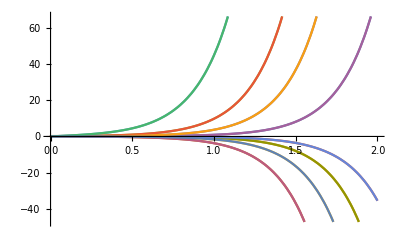

```mathematica
Plot[Evaluate[%],{t,0,2}]
```

## Feedback Linearization

```mathematica
Lf1h1=LieBracketScalar[f,h[[1]],x[t]];
Lf2h1=LieBracketScalar[f,Lf1h1,x[t]];
Lf1h2=LieBracketScalar[f,h[[2]],x[t]];
Lf2h2=LieBracketScalar[f,Lf1h2,x[t]];
(*Lf3h1=LieBracketScalar[f,Lf2h1,x[t]]
Lf3h2=LieBracketScalar[f,Lf2h2,x[t]]*)
```

```mathematica
Γ={Lf3h1,Lf3h2};
```

```mathematica
Lg1Lf1h1=LieBracketScalar[g1trick,Lf1h1,xtrick[t]];
Lg2Lf1h1=LieBracketScalar[g2trick,Lf1h1,xtrick[t]];
Lg1Lf1h2=LieBracketScalar[g1trick,Lf1h2,xtrick[t]];
Lg2Lf1h2=LieBracketScalar[g2trick,Lf1h2,xtrick[t]];
```

```mathematica
Lg1Lf2h1=LieBracketScalar[g1trick,Lf2h1,xtrick[t]];
Lg2Lf2h1=LieBracketScalar[g2trick,Lf2h1,xtrick[t]];
Lg1Lf2h2=LieBracketScalar[g1trick,Lf2h2,xtrick[t]];
Lg2Lf2h2=LieBracketScalar[g2trick,Lf2h2,xtrick[t]];
```

```mathematica
y1'=Lf1h1;
y1''=Lf2h1+Lg1Lf1h1*u[[1]]+Lg2Lf1h1*u[[2]];
y2'=Lf1h2;
y2''=Lf2h2+Lg1Lf1h2*u[[1]]+Lg2Lf1h2*u[[2]];
y1'''=Lf3h1+Lg1Lf2h1*u[[1]]+Lg2Lf2h1*u[[2]];
y2'''=Lf3h2+Lg1Lf2h2*u[[1]]+Lg2Lf2h2*u[[2]];
```

```mathematica
Ε={{Lg1Lf2h1,Lg2Lf2h1},{Lg1Lf2h2,Lg2Lf2h2}};
ξ1={h[[1]],Lf1h1, Lf2h1};
ξ2={h[[2]],Lf1h2, Lf2h2};
ξ = Join[ξ1,ξ2];
```

```mathematica
gtrick=Transpose[Join[{g1trick},{g2trick}]];
```

```mathematica
η1=θl'[t]+θr'[t]
```

θl'[t]+θr'[t]

```mathematica
η1=τsum[t];
η2=θl[t];
η3=θr[t];
```

#### Coordinate change

ηc1 and ηc2 were first chosen and then run through FullSimplify to avoid unnecessary complex values

Verifica dell’indipendenza di η_i dall’ingresso

```mathematica
Simplify[LieBracketScalar[g1trick,η1,xtrick[t]]]
Simplify[LieBracketScalar[g2trick,η1,xtrick[t]]]
Simplify[LieBracketScalar[g1trick,η2,xtrick[t]]]
Simplify[LieBracketScalar[g2trick,η2,xtrick[t]]]
Simplify[LieBracketScalar[g1trick,η3,xtrick[t]]]
Simplify[LieBracketScalar[g2trick,η3,xtrick[t]]]
```

1

0

0

0

«2 more identical outputs»

Verifica della correttezza del cambio di coordinate (risultato: determinante nullo solo in r[t]=0, verifica con Solve[])

```mathematica
Φ=Join[ξ1,ξ2,{η1},{η2},{η3}];
```

```mathematica
Det[D[Φ,{xtrick[t]}]];
```

```mathematica
Solve[Det[D[Φ,{x[t]}]]==0,x[t]]
```

Det::matsq: Argument {{0,0,1,0,0,0,0,0},{0,0,0,0,0,0,1,0},{«1»},{0,0,0,1,0,0,0,0},{«1»},{-(24 (Cos[Times[«3»]] Cos[ϕ[«1»]]+Sin[Times[«3»]] Sin[ϕ[«1»]] Sin[ψ[«1»]]) («1») τsum[t])/(lp r («1»)^2)+«20»+(«1»)/(«1»)-(12 («1») (-(lp «4»)/(4 la)+(«1»)/(4 la)+(«1»)/(4 la)))/(lp r («1»)),-(24 «2» «1»)/(lp r («1»)^2)+«21»,«4»,«1»,«1»},{0,0,0,0,0,0,0,0},{0,1,0,0,0,0,0,0},{1,0,0,0,0,0,0,0}} at position 1 is not a non-empty square matrix.

Solve::nsmet: This system cannot be solved with the methods available to Solve.

Solve[Det[{{0,0,1,0,0,0,0,0},{0,0,0,0,0,0,1,0},5,{0,1,0,0,0,0,0,0},{1,0,0,0,0,0,0,0}}]==0,{θr[t],θl[t],ψ[t],ϕ[t],θr'[t],θl'[t],ψ'[t],ϕ'[t]}]
 |  |  |  |

```mathematica
K1=5*{10,8,1,0,0,0};
K2=5*{0,0,0,10,8,1};
```

```mathematica
α={1,1,1,1,1,1};
```

```mathematica
InvE=Inverse[Ε];
```

```mathematica
ν1= -K1.ξ;
ν2= -K2.ξ;
```

```mathematica
Dimensions[Γ]
```

{2}

```mathematica
u=-InvE.Γ+InvE.{ν1,ν2}
```

{((-((8 la^2 mp+10)/(mr r^2 1(11 (8 mp+9))-1) (1)-1) (1))/(-(12 4)/(lp r (3 mp 1^2+1+1))-(24 (1) (1))/(lp r (1)))+5,4+1}
 |  |  |  |

```mathematica
Dimensions[u]
```

{2}

```mathematica
Dimensions[ ξ]
```

{6}

```mathematica
Dimensions[u[[1]]]
```

{4}

#### Zero dynamics

```mathematica
η = {ϕ1[t],ϕ2[t],ϕ1'[t],ϕ2'[t]};
```

f + g*u = f + g*(α + β*ν[t]) = (f + g*α) + g*β*ν[t] = f_fl + g_fl*ν[t]

```mathematica
Dimensions[ffl]
```

{}

```mathematica
ffl = Simplify[f+ArrayReshape[g*α[[1]],{6}]];
gfl =Simplify[g*β[[1]]];
```

Thread::tdlen: Objects of unequal length in {θr'[t],θl'[t],«4»,«1»,-(9 «4» (-1/2 G lp mp Cos[ϕ[«1»]] Sin[ψ[«1»]]+(lp mp «3» «1» ((«1»)^(«1»)«1»«1»])^2)/(4 la)-(lp «5» («1»)^2)/(4 la)-1/3 lp^2 mp Sin[Times[«2»]] ϕ'[t] ψ'[t]))/(lp^2 (3 mp Power[«2»]+Power[«2»] Plus[«2»]+3 mp Sin[«1»] Tan[«1»] Plus[«2»]))-(«1»)/(lp^2 mp («1»))-(«1»)/(«1»)-(12 («1») (-(lp «3» («1»+«1»))/(4 la)+(«1»)/(«1»)+(«1»)/(4 la)))/(lp r («1»))}+{«1»} cannot be combined.

$Aborted

Part::partd: Part specification β⟦1⟧ is longer than depth of object.

```mathematica
Dimensions[gfl]
```

{8,2}

## Solve Diff. Equations

### ODEs integration

```mathematica
tsim=20;
DynEqs={
 SysPointEqns[[5]],
SysPointEqns[[6]],
 SysPointEqns[[7]],
 SysPointEqns[[8]],
SysPointEqns[[9]]
};
DynEqs2={
0==DynLeftTerm[[1]],
0==DynLeftTerm[[2]],
0==DynLeftTerm[[3]],
0==DynLeftTerm[[4]]
};
DynEqs3={
 SysPointEqns2[[5]],
SysPointEqns2[[6]],
 SysPointEqns2[[7]],
 SysPointEqns2[[8]]
};
InitialConditions={
θr[0]==0.,
θl[0]==0.,
ψ[0]==0,
ϕ[0]==0,
θr'[0]==200,
θl'[0]==0,
ψ'[0]==0,
ϕ'[0]==0
};
```

```mathematica
pendulumsolutionnormalform=NDSolveValue[
Join[DynEqs3,InitialConditions]/.params,
{θr,θl,ψ,ϕ},
{t,0,tsim}]
```

NDSolveValue::ndsz: At t == 0.0000442148, step size is effectively zero; singularity or stiff system suspected.

{InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…]}

### Integrate for X and Y

```mathematica
tsim=0.000044214797516648465
sol1=pendulumsolutionnormalform[[1]];
sol2=pendulumsolutionnormalform[[2]];
sol3=pendulumsolutionnormalform[[3]];
sol4=pendulumsolutionnormalform[[4]];
solution={θr->sol1,θl->sol2,ψ->sol3,ϕ->sol4,θr'->sol1',θl'->sol2',ψ'->sol3',ϕ'->sol4' };
xdnum=xd/.solution/.params;
ydnum=yd/.solution/.params;
xnumerical=NDSolveValue[{xnum'[t]== xdnum,xnum[0]== 0},{xnum},{t,0,tsim}];
ynumerical=NDSolveValue[{ynum'[t]== ydnum,ynum[0]== 0},{ynum},{t,0,tsim}];
solutions=Join[solution,{x-> First[xnumerical], y-> First[ynumerical]}];
solutions
```

0.0000442148

{θr→InterpolatingFunction[…],θl→InterpolatingFunction[…],ψ→InterpolatingFunction[…],ϕ→InterpolatingFunction[…],θr'→InterpolatingFunction[…],θl'→InterpolatingFunction[…],ψ'→InterpolatingFunction[…],ϕ'→InterpolatingFunction[…],x→InterpolatingFunction[…],y→InterpolatingFunction[…]}

### Plot Total Energy

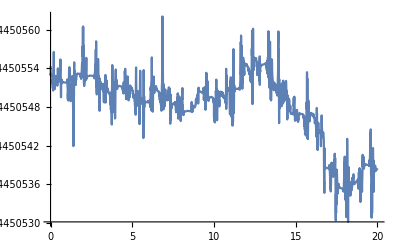

```mathematica
Plot[{U+Etot}/.solution/.params,{t,0,tsim}]
```

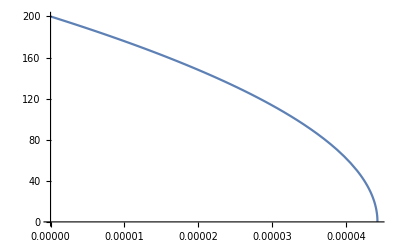

```mathematica
Plot[(θr'[t]+θl'[t])/.solutions,{t,0,tsim}]
```

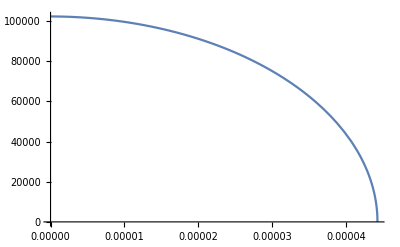

```mathematica
Plot[Det[Ε]/.solutions/.params,{t,0,tsim}]
```

## Simulation

```mathematica
Clear[η]
```

```mathematica
Rz[ϵ_]=RotationMatrix[ϵ,{0,0,1}];
Ry[ϵ_]=RotationMatrix[ϵ,{0,1,0}];
Rx[ϵ_]=RotationMatrix[ϵ,{1,0,0}];
Rp=Rx[ψ].Ry[ϕ].Rz[η];
R1g=Rx[ψ];
R2g=Rx[ψ].Ry[ϕ];
R3g=Rx[ψ].Ry[ϕ].Rz[η];
Rg1=Transpose[R1g];
Rg2=Transpose[R2g];
Rg3=Transpose[R3g];

orig={0,0,0};
fixedframe={{1,0,0},{0,1,0},{0,0,1}};
OA={x,y,r}/.params;
AP=Rp.{0,0,lp/2};
θ=(r (-θl+θr))/la;
pendulumframe=Rz[(r (-θl+θr))/la].Rx[ψ].Ry[ϕ];
axialframe=Rz[θ];
```

```mathematica
Fixedframe=Arrow[{orig,#}]&/@fixedframe;
Axialframe[θr_,θl_,ψ_,ϕ_,x_,y_]=Arrow[{{x,y,r}/.params,#}]&/@{{x,y,r}+Rz[(r (-θl+θr))/la].{1,0,0},{x,y,r}+Rz[(r (-θl+θr))/la].{0,1,0},
{x,y,r}+{0,0,1}}/.params;
Pendulumframe[θr_,θl_,ψ_,ϕ_,x_,y_]=Arrow[{{x,y,r}/.params,#}]&/@{{x,y,r}+Rz[(r (-θl+θr))/la].Rx[ψ].Ry[ϕ].{1,0,0},
{x,y,r}+Rz[(r (-θl+θr))/la].Rx[ψ].Ry[ϕ].{0,1,0},{x,y,r}+Rz[(r (-θl+θr))/la].Rx[ψ].Ry[ϕ].{0,0,1}
}/.params;
Axial[θr_,θl_,ψ_,ϕ_,x_,y_]=Cylinder[
{{x,y,r}+la/2*Rz[(r (-θl+θr))/la].{0,1,0},
{x,y,r}-la/2*Rz[(r (-θl+θr))/la].{0,1,0}
}/.params,0.01];
Wheel1[θr_,θl_,ψ_,ϕ_,x_,y_]=Cylinder[
{{x,y,r}+0.5*Rz[(r (-θl+θr))/la].{0,1,0},
{x,y,r}+0.6*Rz[(r (-θl+θr))/la].{0,1,0}
}/.params,0.3];
Wheel2[θr_,θl_,ψ_,ϕ_,x_,y_]=Cylinder[
{{x,y,r}-0.5*Rz[(r (-θl+θr))/la].{0,1,0},
{x,y,r}-0.6*Rz[(r (-θl+θr))/la].{0,1,0}
}/.params,0.3];
Pendulum[θr_,θl_,ψ_,ϕ_,x_,y_]=Cylinder[
{{x,y,r},
{x,y,r}+Rz[(r (-θl+θr))/la].Rx[ψ].Ry[ϕ].{0,0,lp}
}/.params,0.05];
```

```mathematica
labels={
MapThread[Text[#1,#2]&,{Style[#,12]&/@{"x","y","z"},1.1 fixedframe}]};
animation[θr_,θl_,ψ_,ϕ_,x_, y_]:=Show[
{
Graphics3D[
{
Fixedframe,
{Orange,Pendulumframe[θr,θl,ψ,ϕ,x,y]},
{Purple,Axialframe[θr,θl,ψ,ϕ,x,y]},
Axial[θr,θl,ψ,ϕ,x,y],
{Yellow,Wheel1[θr,θl,ψ,ϕ,x,y]},
{Yellow,Wheel2[θr,θl,ψ,ϕ,x,y]},
{Blue,Pendulum[θr,θl,ψ,ϕ,x,y]},
{Red,Sphere[{x,y ,0.3},0.08]},
{Red,Sphere[({x,y,r}+Rz[(r (-θl+θr))/la].Rx[ψ].Ry[ϕ].{0,0,lp})/.params,0.08]},
{Opacity[0.2],Polygon[{{x-2,y-2,0},{x-2,y+2,0},{x+2,y+2,0},{x+2,y-2,0}}]}
},
PlotRange->{{x-2,x+2},{y-2,y+2},{-1,2}},
Boxed->False]
}
]
```

## Animation

```mathematica
Clear[x]
Animate[
animation[
First[Evaluate[{θr[t]}/.solutions]],First[Evaluate[{θl[t]}/.solutions]],First[Evaluate[{ψ[t]}/.solutions]],
First[Evaluate[{ϕ[t]}/.solutions]],
First[Evaluate[{x[t]}/.solutions]],
First[Evaluate[{y[t]}/.solutions]]]
 ,
{t,0,tsim}
]
```

## Random Shit

```mathematica
arc1=Table[RotationMatrix[j,{0,0,1}].{0.5,0,0},{j,0,Pi/4,0.01}];
ang=VectorAngle[{0,0,1},{1,1,1}];
axis=Cross[{0,0,1},{1,1,1}];
arc2=Table[RotationMatrix[j,axis].{0,0,0.5},{j,0,ang,0.01}];
labels={Text[Style["θ",12],RotationMatrix[ang/2,axis].{0,0,0.6}],Text[Style["ϕ",12],RotationMatrix[Pi/8,{0,0,1}].{0.6,0,0}],Text[Style[TraditionalForm["r"],12],(orig+pt)/2+{0,0,-0.05}],Text[Style["P",Italic,12],1.1 pt],Text[Column[{"(x,y,z)","(r,θ,ϕ)"}],1.2 pt-{0,0,0.1}],MapThread[Text[#1,#2]&,{Style[#,12]&/@{"x","y","z"},1.1 axes}]}
```

MapThread::mptd: Object 1.1 axes at position {2, 2} in MapThread[Text[#1,#2]&,{{x,y,z},1.1 axes}] has only 0 of required 1 dimensions.

{Text[θ,{0.195035,0.195035,0.532844}],Text[ϕ,{0.554328,0.22961,0.}],Text[r,{pt/2,pt/2,-0.05+pt/2}],Text[P,1.1 pt],Text[(x,y,z)
(r,θ,ϕ),{1.2 pt,1.2 pt,-0.1+1.2 pt}],MapThread[Text[#1,#2]&,{{x,y,z},1.1 axes}]}

```mathematica
Graphics3D[
{
Arrow[{orig,#}]&/@axes,
{Red,Arrow[{orig,pt}]},Line[{orig,{0.5,0.5,0}}],Line[{{0.5,0.5,0},{0.5,0.5,0.5}}],Line[arc1],Line[arc2],{Opacity[0.2],Polygon[{orig,{1,0,0},{1,0,1},{0,0,1}}]},{Opacity[0.2],Polygon[{orig,{0,1,0},{0,1,1},{0,0,1}}]},
labels
},
Boxed->False]
```

-Graphics3D-

## Feedback Linearization with Energy and distance

```mathematica
Etot;
```

```mathematica
hs = {Emec,(θr'[t])^2+(θl'[t])^2};
```

```mathematica
us = {τsum[t], τdiff[t]};
xs[t]=x[t];
fs=f;
g1s=g1+g2;
g2s=g1-g2;
gs = Transpose[Simplify[{g1s,g2s}]];
```

```mathematica
Lf1h1=LieBracketScalar[fs,hs[[1]],xs[t]];
Lf1h2=LieBracketScalar[fs,hs[[2]],xs[t]];
```

```mathematica
Lg1h1=Simplify[LieBracketScalar[g1s,hs[[1]],xs[t]]]
Lg2h1=Simplify[LieBracketScalar[g2s,hs[[1]],xs[t]]]
Lg1h2=Simplify[LieBracketScalar[g1s,hs[[2]],xs[t]]]
Lg2h2=Simplify[LieBracketScalar[g2s,hs[[2]],xs[t]]]
```

((68 mp+384 mr+12 mp Cos[(2 r (-θl[t]+θr[t]))/la]-18 mp Cos[(2 r (-θl[t]+θr[t]))/la-2 ϕ[t]]-12 mp Cos[2 ϕ[t]]-18 mp Cos[2 ((r (-θl[t]+θr[t]))/la+ϕ[t])]+6 mp Cos[(2 r (-θl[t]+θr[t]))/la-2 ψ[t]]-6 mp Cos[2 (ϕ[t]-ψ[t])]+3 mp Cos[2 ((r (-θl[t]+θr[t]))/la+ϕ[t]-ψ[t])]-12 mp Cos[2 ψ[t]]+6 mp Cos[2 ((r (-θl[t]+θr[t]))/la+ψ[t])]+3 mp Cos[2 ((r (-θl[t]+θr[t]))/la-ϕ[t]+ψ[t])]-6 mp Cos[2 (ϕ[t]+ψ[t])]+3 mp Cos[2 ((r (-θl[t]+θr[t]))/la+ϕ[t]+ψ[t])]+3 mp Cos[(2 (r θl[t]-r θr[t]+la (ϕ[t]+ψ[t])))/la]+12 mp Sin[(2 r (-θl[t]+θr[t]))/la-2 ϕ[t]-ψ[t]]-12 mp Sin[(2 r (-θl[t]+θr[t]))/la+2 ϕ[t]-ψ[t]]-12 mp Sin[(2 r (-θl[t]+θr[t]))/la-2 ϕ[t]+ψ[t]]+12 mp Sin[(2 r (-θl[t]+θr[t]))/la+2 ϕ[t]+ψ[t]])^2 (θl'[t]+θr'[t]))/(512 (-4 mp-12 mr+3 mp Cos[(r (-θl[t]+θr[t]))/la]^2 Cos[ϕ[t]]^2+3 mp Cos[ψ[t]]^2 Sin[(r (-θl[t]+θr[t]))/la]^2+3 mp Cos[ϕ[t]] Sin[(2 r (-θl[t]+θr[t]))/la] Sin[ϕ[t]] Sin[ψ[t]]+3 mp Sin[(r (-θl[t]+θr[t]))/la]^2 Sin[ϕ[t]]^2 Sin[ψ[t]]^2) (-8 mp-24 mr+6 mp Cos[(r (-θl[t]+θr[t]))/la]^2 Cos[ϕ[t]]^2+6 mp Cos[ψ[t]]^2 Sin[(r (-θl[t]+θr[t]))/la]^2+3 mp Sin[(2 r (-θl[t]+θr[t]))/la] Sin[2 ϕ[t]] Sin[ψ[t]]+6 mp Sin[(r (-θl[t]+θr[t]))/la]^2 Sin[ϕ[t]]^2 Sin[ψ[t]]^2))

-θl'[t]+θr'[t]

-((32 (θl'[t]+θr'[t]))/(r^2 (-8 mp-24 mr+6 mp Cos[(r (-θl[t]+θr[t]))/la]^2 Cos[ϕ[t]]^2+6 mp Cos[ψ[t]]^2 Sin[(r (-θl[t]+θr[t]))/la]^2+3 mp Sin[(2 r (-θl[t]+θr[t]))/la] Sin[2 ϕ[t]] Sin[ψ[t]]+6 mp Sin[(r (-θl[t]+θr[t]))/la]^2 Sin[ϕ[t]]^2 Sin[ψ[t]]^2)))

-(4 la^2 (θl'[t]-θr'[t]))/(mr r^2 (3 la^2+2 r^2))

```mathematica
y1'=Lf1h1+Lg1h1+Lg2h1;
y2'=Lf1h2+Lg1h2+Lg2h2;
```

```mathematica
Γ={Lf1h1,Lf1h2};
```

```mathematica
Ε={{Lg1h1,Lg2h1},{Lg1h2,Lg2h2}};
ξ1={hs[[1]]};
ξ2={hs[[2]]};
ξs = Join[ξ1,ξ2];
```

```mathematica
η1=ψ[t];
η2=ψ'[t];
η3=ϕ[t];
η4=ϕ'[t];
η5=θr[t];
η6=θl[t];
```

#### Coordinate change

ηc1 and ηc2 were first chosen and then run through FullSimplify to avoid unnecessary complex values

Verifica dell’indipendenza di η_i dall’ingresso

```mathematica
Simplify[LieBracketScalar[g1,η1,x[t]]];
Simplify[LieBracketScalar[g2,η1,x[t]]];
Simplify[LieBracketScalar[g1,η2,x[t]]]
Simplify[LieBracketScalar[g2,η2,x[t]]]
Simplify[LieBracketScalar[g1,η3,x[t]]];
Simplify[LieBracketScalar[g2,η3,x[t]]];
Simplify[LieBracketScalar[g1,η4,x[t]]]
Simplify[LieBracketScalar[g2,η4,x[t]]]
Simplify[LieBracketScalar[g1,η5,x[t]]];
Simplify[LieBracketScalar[g2,η5,x[t]]];
Simplify[LieBracketScalar[g1,η6,x[t]]];
Simplify[LieBracketScalar[g2,η6,x[t]]];
```

-((6 Cos[ψ[t]] Sec[ϕ[t]]^3 Sin[(r (-θl[t]+θr[t]))/la])/(lp r (3 mp Cos[(r (-θl[t]+θr[t]))/la]^2+Sec[ϕ[t]]^2 (-4 (mp+3 mr)+3 mp Cos[ψ[t]]^2 Sin[(r (-θl[t]+θr[t]))/la]^2)+3 mp Sin[ψ[t]] Tan[ϕ[t]] (Sin[(2 r (-θl[t]+θr[t]))/la]+Sin[(r (-θl[t]+θr[t]))/la]^2 Sin[ψ[t]] Tan[ϕ[t]]))))

-((6 Cos[ψ[t]] Sec[ϕ[t]]^3 Sin[(r (-θl[t]+θr[t]))/la])/(lp r (3 mp Cos[(r (-θl[t]+θr[t]))/la]^2+Sec[ϕ[t]]^2 (-4 (mp+3 mr)+3 mp Cos[ψ[t]]^2 Sin[(r (-θl[t]+θr[t]))/la]^2)+3 mp Sin[ψ[t]] Tan[ϕ[t]] (Sin[(2 r (-θl[t]+θr[t]))/la]+Sin[(r (-θl[t]+θr[t]))/la]^2 Sin[ψ[t]] Tan[ϕ[t]]))))

(12 (Cos[(r (-θl[t]+θr[t]))/la] Cos[ϕ[t]]+Sin[(r (-θl[t]+θr[t]))/la] Sin[ϕ[t]] Sin[ψ[t]]))/(lp r (-8 mp-24 mr+6 mp Cos[(r (-θl[t]+θr[t]))/la]^2 Cos[ϕ[t]]^2+6 mp Cos[ψ[t]]^2 Sin[(r (-θl[t]+θr[t]))/la]^2+3 mp Sin[(2 r (-θl[t]+θr[t]))/la] Sin[2 ϕ[t]] Sin[ψ[t]]+6 mp Sin[(r (-θl[t]+θr[t]))/la]^2 Sin[ϕ[t]]^2 Sin[ψ[t]]^2))

(12 (Cos[(r (-θl[t]+θr[t]))/la] Cos[ϕ[t]]+Sin[(r (-θl[t]+θr[t]))/la] Sin[ϕ[t]] Sin[ψ[t]]))/(lp r (-8 mp-24 mr+6 mp Cos[(r (-θl[t]+θr[t]))/la]^2 Cos[ϕ[t]]^2+6 mp Cos[ψ[t]]^2 Sin[(r (-θl[t]+θr[t]))/la]^2+3 mp Sin[(2 r (-θl[t]+θr[t]))/la] Sin[2 ϕ[t]] Sin[ψ[t]]+6 mp Sin[(r (-θl[t]+θr[t]))/la]^2 Sin[ϕ[t]]^2 Sin[ψ[t]]^2))

Verifica della correttezza del cambio di coordinate (risultato: determinante nullo solo in r[t]=0, verifica con Solve[])

```mathematica
Φ=Join[ξ1,ξ2,{η1},{η2},{η3},{η4},{η5},{η6}];
```

```mathematica
Det[D[Φ,{x[t]}]]
```

2 (-1/4 mp r^2 θl'[t]^2+(mr r^4 θl'[t]^2)/(2 la^2)+1/4 mp r^2 θr'[t]^2-(mr r^4 θr'[t]^2)/(2 la^2)-1/4 lp mp r Cos[(r (-θl[t]+θr[t]))/la] Cos[ϕ[t]] θl'[t] ϕ'[t]-1/4 lp mp r Sin[(r (-θl[t]+θr[t]))/la] Sin[ϕ[t]] Sin[ψ[t]] θl'[t] ϕ'[t]+1/4 lp mp r Cos[(r (-θl[t]+θr[t]))/la] Cos[ϕ[t]] θr'[t] ϕ'[t]+1/4 lp mp r Sin[(r (-θl[t]+θr[t]))/la] Sin[ϕ[t]] Sin[ψ[t]] θr'[t] ϕ'[t]+1/4 lp mp r Cos[ϕ[t]] Cos[ψ[t]] Sin[(r (-θl[t]+θr[t]))/la] θl'[t] ψ'[t]-1/4 lp mp r Cos[ϕ[t]] Cos[ψ[t]] Sin[(r (-θl[t]+θr[t]))/la] θr'[t] ψ'[t])

```mathematica
Solve[Det[D[Φ,{x[t]}]]==0,x[t]]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

Solve::svars: Equations may not give solutions for all "solve" variables.

{{θl'[t]→θr'[t]}}

```mathematica
K1=5*{10,8};
K2=5*{10,8};
```

```mathematica
InvE=Inverse[Ε];
```

```mathematica
Det[InvE]
```

```mathematica
Simplify[Ε]//MatrixForm
```

(((68 mp+384 mr+12 mp Cos[(2 r (-θl[t]+θr[t]))/la]-18 mp Cos[(2 r (-θl[t]+θr[t]))/la-2 ϕ[t]]-12 mp Cos[2 ϕ[t]]-18 mp Cos[2 ((r (-θl[t]+θr[t]))/la+ϕ[t])]+6 mp Cos[(2 r (-θl[t]+θr[t]))/la-2 ψ[t]]-6 mp Cos[2 (ϕ[t]-ψ[t])]+3 mp Cos[2 ((r (-θl[t]+θr[t]))/la+ϕ[t]-ψ[t])]-12 mp Cos[2 ψ[t]]+6 mp Cos[2 ((r (-θl[t]+θr[t]))/la+ψ[t])]+3 mp Cos[2 ((r (-θl[t]+θr[t]))/la-ϕ[t]+ψ[t])]-6 mp Cos[2 (ϕ[t]+ψ[t])]+3 mp Cos[2 ((r (-θl[t]+θr[t]))/la+ϕ[t]+ψ[t])]+3 mp Cos[(2 (r θl[t]-r θr[t]+la (ϕ[t]+ψ[t])))/la]+12 mp Sin[(2 r (-θl[t]+θr[t]))/la-2 ϕ[t]-ψ[t]]-12 mp Sin[(2 r (-θl[t]+θr[t]))/la+2 ϕ[t]-ψ[t]]-12 mp Sin[(2 r (-θl[t]+θr[t]))/la-2 ϕ[t]+ψ[t]]+12 mp Sin[(2 r (-θl[t]+θr[t]))/la+2 ϕ[t]+ψ[t]])^2 θr'[t])/(512 (-4 mp-12 mr+3 mp Cos[(r (-θl[t]+θr[t]))/la]^2 Cos[ϕ[t]]^2+3 mp Cos[ψ[t]]^2 Sin[(r (-θl[t]+θr[t]))/la]^2+3 mp Cos[ϕ[t]] Sin[(2 r (-θl[t]+θr[t]))/la] Sin[ϕ[t]] Sin[ψ[t]]+3 mp Sin[(r (-θl[t]+θr[t]))/la]^2 Sin[ϕ[t]]^2 Sin[ψ[t]]^2) (-8 mp-24 mr+6 mp Cos[(r (-θl[t]+θr[t]))/la]^2 Cos[ϕ[t]]^2+6 mp Cos[ψ[t]]^2 Sin[(r (-θl[t]+θr[t]))/la]^2+3 mp Sin[(2 r (-θl[t]+θr[t]))/la] Sin[2 ϕ[t]] Sin[ψ[t]]+6 mp Sin[(r (-θl[t]+θr[t]))/la]^2 Sin[ϕ[t]]^2 Sin[ψ[t]]^2)) | ((68 mp+384 mr+12 mp Cos[(2 r (-θl[t]+θr[t]))/la]-18 mp Cos[(2 r (-θl[t]+θr[t]))/la-2 ϕ[t]]-12 mp Cos[2 ϕ[t]]-18 mp Cos[2 ((r (-θl[t]+θr[t]))/la+ϕ[t])]+6 mp Cos[(2 r (-θl[t]+θr[t]))/la-2 ψ[t]]-6 mp Cos[2 (ϕ[t]-ψ[t])]+3 mp Cos[2 ((r (-θl[t]+θr[t]))/la+ϕ[t]-ψ[t])]-12 mp Cos[2 ψ[t]]+6 mp Cos[2 ((r (-θl[t]+θr[t]))/la+ψ[t])]+3 mp Cos[2 ((r (-θl[t]+θr[t]))/la-ϕ[t]+ψ[t])]-6 mp Cos[2 (ϕ[t]+ψ[t])]+3 mp Cos[2 ((r (-θl[t]+θr[t]))/la+ϕ[t]+ψ[t])]+3 mp Cos[(2 (r θl[t]-r θr[t]+la (ϕ[t]+ψ[t])))/la]+12 mp Sin[(2 r (-θl[t]+θr[t]))/la-2 ϕ[t]-ψ[t]]-12 mp Sin[(2 r (-θl[t]+θr[t]))/la+2 ϕ[t]-ψ[t]]-12 mp Sin[(2 r (-θl[t]+θr[t]))/la-2 ϕ[t]+ψ[t]]+12 mp Sin[(2 r (-θl[t]+θr[t]))/la+2 ϕ[t]+ψ[t]])^2 θl'[t])/(512 (-4 mp-12 mr+3 mp Cos[(r (-θl[t]+θr[t]))/la]^2 Cos[ϕ[t]]^2+3 mp Cos[ψ[t]]^2 Sin[(r (-θl[t]+θr[t]))/la]^2+3 mp Cos[ϕ[t]] Sin[(2 r (-θl[t]+θr[t]))/la] Sin[ϕ[t]] Sin[ψ[t]]+3 mp Sin[(r (-θl[t]+θr[t]))/la]^2 Sin[ϕ[t]]^2 Sin[ψ[t]]^2) (-8 mp-24 mr+6 mp Cos[(r (-θl[t]+θr[t]))/la]^2 Cos[ϕ[t]]^2+6 mp Cos[ψ[t]]^2 Sin[(r (-θl[t]+θr[t]))/la]^2+3 mp Sin[(2 r (-θl[t]+θr[t]))/la] Sin[2 ϕ[t]] Sin[ψ[t]]+6 mp Sin[(r (-θl[t]+θr[t]))/la]^2 Sin[ϕ[t]]^2 Sin[ψ[t]]^2))
((68 mp+384 mr+12 mp Cos[(2 r (-θl[t]+θr[t]))/la]-18 mp Cos[(2 r (-θl[t]+θr[t]))/la-2 ϕ[t]]-12 mp Cos[2 ϕ[t]]-18 mp Cos[2 ((r (-θl[t]+θr[t]))/la+ϕ[t])]+6 mp Cos[(2 r (-θl[t]+θr[t]))/la-2 ψ[t]]-6 mp Cos[2 (ϕ[t]-ψ[t])]+3 mp Cos[2 ((r (-θl[t]+θr[t]))/la+ϕ[t]-ψ[t])]-12 mp Cos[2 ψ[t]]+6 mp Cos[2 ((r (-θl[t]+θr[t]))/la+ψ[t])]+3 mp Cos[2 ((r (-θl[t]+θr[t]))/la-ϕ[t]+ψ[t])]-6 mp Cos[2 (ϕ[t]+ψ[t])]+3 mp Cos[2 ((r (-θl[t]+θr[t]))/la+ϕ[t]+ψ[t])]+3 mp Cos[(2 (r θl[t]-r θr[t]+la (ϕ[t]+ψ[t])))/la]+12 mp Sin[(2 r (-θl[t]+θr[t]))/la-2 ϕ[t]-ψ[t]]-12 mp Sin[(2 r (-θl[t]+θr[t]))/la+2 ϕ[t]-ψ[t]]-12 mp Sin[(2 r (-θl[t]+θr[t]))/la-2 ϕ[t]+ψ[t]]+12 mp Sin[(2 r (-θl[t]+θr[t]))/la+2 ϕ[t]+ψ[t]])^2 θr'[t])/(512 (-4 mp-12 mr+3 mp Cos[(r (-θl[t]+θr[t]))/la]^2 Cos[ϕ[t]]^2+3 mp Cos[ψ[t]]^2 Sin[(r (-θl[t]+θr[t]))/la]^2+3 mp Cos[ϕ[t]] Sin[(2 r (-θl[t]+θr[t]))/la] Sin[ϕ[t]] Sin[ψ[t]]+3 mp Sin[(r (-θl[t]+θr[t]))/la]^2 Sin[ϕ[t]]^2 Sin[ψ[t]]^2) (-8 mp-24 mr+6 mp Cos[(r (-θl[t]+θr[t]))/la]^2 Cos[ϕ[t]]^2+6 mp Cos[ψ[t]]^2 Sin[(r (-θl[t]+θr[t]))/la]^2+3 mp Sin[(2 r (-θl[t]+θr[t]))/la] Sin[2 ϕ[t]] Sin[ψ[t]]+6 mp Sin[(r (-θl[t]+θr[t]))/la]^2 Sin[ϕ[t]]^2 Sin[ψ[t]]^2)) | ((68 mp+384 mr+12 mp Cos[(2 r (-θl[t]+θr[t]))/la]-18 mp Cos[(2 r (-θl[t]+θr[t]))/la-2 ϕ[t]]-12 mp Cos[2 ϕ[t]]-18 mp Cos[2 ((r (-θl[t]+θr[t]))/la+ϕ[t])]+6 mp Cos[(2 r (-θl[t]+θr[t]))/la-2 ψ[t]]-6 mp Cos[2 (ϕ[t]-ψ[t])]+3 mp Cos[2 ((r (-θl[t]+θr[t]))/la+ϕ[t]-ψ[t])]-12 mp Cos[2 ψ[t]]+6 mp Cos[2 ((r (-θl[t]+θr[t]))/la+ψ[t])]+3 mp Cos[2 ((r (-θl[t]+θr[t]))/la-ϕ[t]+ψ[t])]-6 mp Cos[2 (ϕ[t]+ψ[t])]+3 mp Cos[2 ((r (-θl[t]+θr[t]))/la+ϕ[t]+ψ[t])]+3 mp Cos[(2 (r θl[t]-r θr[t]+la (ϕ[t]+ψ[t])))/la]+12 mp Sin[(2 r (-θl[t]+θr[t]))/la-2 ϕ[t]-ψ[t]]-12 mp Sin[(2 r (-θl[t]+θr[t]))/la+2 ϕ[t]-ψ[t]]-12 mp Sin[(2 r (-θl[t]+θr[t]))/la-2 ϕ[t]+ψ[t]]+12 mp Sin[(2 r (-θl[t]+θr[t]))/la+2 ϕ[t]+ψ[t]])^2 θl'[t])/(512 (-4 mp-12 mr+3 mp Cos[(r (-θl[t]+θr[t]))/la]^2 Cos[ϕ[t]]^2+3 mp Cos[ψ[t]]^2 Sin[(r (-θl[t]+θr[t]))/la]^2+3 mp Cos[ϕ[t]] Sin[(2 r (-θl[t]+θr[t]))/la] Sin[ϕ[t]] Sin[ψ[t]]+3 mp Sin[(r (-θl[t]+θr[t]))/la]^2 Sin[ϕ[t]]^2 Sin[ψ[t]]^2) (-8 mp-24 mr+6 mp Cos[(r (-θl[t]+θr[t]))/la]^2 Cos[ϕ[t]]^2+6 mp Cos[ψ[t]]^2 Sin[(r (-θl[t]+θr[t]))/la]^2+3 mp Sin[(2 r (-θl[t]+θr[t]))/la] Sin[2 ϕ[t]] Sin[ψ[t]]+6 mp Sin[(r (-θl[t]+θr[t]))/la]^2 Sin[ϕ[t]]^2 Sin[ψ[t]]^2)))

```mathematica
ν1= -K1.ξs;
ν2= -K2.ξs;
```

```mathematica
u=-InvE.Γ+InvE.{ν1,ν2}
```

{((θl'[t]-θr'[t]) (-40 (θl'[t]^2+θr'[t]^2)-50 (1/2 G lp mp Cos[ϕ[t]] Cos[ψ[t]]+1)))/(-(la^2 (1)^2 (1) (θl'[t]+θr'[t]))/(128 4 (6+6 3 1^2))+1/1)-1/1-1+(4 la^2 1 (1))/1,1}
 |  |  |  |

```mathematica
Simplify[Det[Simplify[Ε/.{θr'[t]-> θl'[t]}]]]
```

```mathematica
CorrespondenceListSysPointEquation2=Join[{D[x[t],t]},{fs+gs.u}];
SysPointEqns2= MakeEqual[#[[1]], #[[2]]]&/@Transpose[CorrespondenceListSysPointEquation2];
```